#### Steering distillation

```mathematica
c2=√(1-c0^2-c1^2);
NMinimize[{(9/2 c2^2+3/2+3c0 c1-6c1 c2-6c2 c0)+(1/4-9/4 c2^2+9/4 c2^2(c0+c1)^2-3/2 c0 c1),0<c0<1/(√3),0<c1≤1/(√3)},{c0,c1}]
NMaximize[{(9/2 c2^2+3/2+3c0 c1-6c1 c2-6c2 c0)+(1/4-9/4 c2^2+9/4 c2^2(c0+c1)^2-3/2 c0 c1),0<c0<1/(√3),0<c1≤1/(√3)},{c0,c1}]
Clear[c2]
```

{-8.88178×10^-16,{c0→0.57735,c1→0.57735}}

{4.,{c0→0.,c1→0.}}

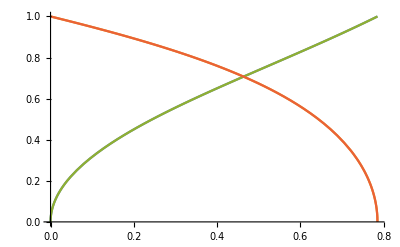

```mathematica
Plot[{(Tan[x])^(1/2),√(1-(Tan[x])),(Tan[x])^((-1+2)/2),√(1-Tan[x]^(2-2/2))},{x,0,π/4}]
```

```mathematica
Array[σ,4,0];
σ[0]=({{1, 0}, {0, 1}});
σ[1]=PauliMatrix[1];
σ[2]=PauliMatrix[2];
σ[3]=PauliMatrix[3];
σ[0,0]={{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}};
```

```mathematica
u={{1},{0}};
d=({{0},{1}});
uu={1,0,0,0};
ud={0,1,0,0};
du={0,0,1,0};
dd={0,0,0,1};
p=Simplify[Cos[θ]u+ι Sin[θ]d];
m=Simplify[Cos[θ]u-ι Sin[θ]d];
ut=ConjugateTranspose[u];
dt=ConjugateTranspose[d];
pt=Simplify[ConjugateTranspose[p],0<θ<π];
mt=Simplify[ConjugateTranspose[m],0<θ<π];
MatrixForm[ut]
```

(1 | 0)

```mathematica
MatrixForm[p.pt]
```

(Cos[θ]^2 | Conjugate[ι] Cos[θ] Sin[θ]
ι Cos[θ] Sin[θ] | ι Conjugate[ι] Sin[θ]^2)

```mathematica
A=({{a1, a2}, {a3, a4}});B=({{b1, b2}, {b3, b4}});F=({{f1, f2}, {f3, f4}});
MatrixForm[Simplify[KroneckerProduct[A,B,F]]]
```

(a1 b1 f1 | a1 b1 f2 | a1 b2 f1 | a1 b2 f2 | a2 b1 f1 | a2 b1 f2 | a2 b2 f1 | a2 b2 f2
a1 b1 f3 | a1 b1 f4 | a1 b2 f3 | a1 b2 f4 | a2 b1 f3 | a2 b1 f4 | a2 b2 f3 | a2 b2 f4
a1 b3 f1 | a1 b3 f2 | a1 b4 f1 | a1 b4 f2 | a2 b3 f1 | a2 b3 f2 | a2 b4 f1 | a2 b4 f2
a1 b3 f3 | a1 b3 f4 | a1 b4 f3 | a1 b4 f4 | a2 b3 f3 | a2 b3 f4 | a2 b4 f3 | a2 b4 f4
a3 b1 f1 | a3 b1 f2 | a3 b2 f1 | a3 b2 f2 | a4 b1 f1 | a4 b1 f2 | a4 b2 f1 | a4 b2 f2
a3 b1 f3 | a3 b1 f4 | a3 b2 f3 | a3 b2 f4 | a4 b1 f3 | a4 b1 f4 | a4 b2 f3 | a4 b2 f4
a3 b3 f1 | a3 b3 f2 | a3 b4 f1 | a3 b4 f2 | a4 b3 f1 | a4 b3 f2 | a4 b4 f1 | a4 b4 f2
a3 b3 f3 | a3 b3 f4 | a3 b4 f3 | a3 b4 f4 | a4 b3 f3 | a4 b3 f4 | a4 b4 f3 | a4 b4 f4)

```mathematica
ψg=Simplify[Cos[θ](KroneckerProduct[u,u,u])+Sin[θ](KroneckerProduct[d,d,d])];
ψgT=Simplify[ConjugateTranspose[ψg],0<θ<π];
ρg=Simplify[v ψg.ψgT+(1-v)σ[0,0]/8];
MatrixForm[ρg]
Simplify[Tr[ρg]]
```

(1/8 (1+3 v+4 v Cos[2 θ]) | 0 | 0 | 0 | 0 | 0 | 0 | v Cos[θ] Sin[θ]
0 | (1-v)/8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-v)/8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (1-v)/8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (1-v)/8 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (1-v)/8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (1-v)/8 | 0
v Cos[θ] Sin[θ] | 0 | 0 | 0 | 0 | 0 | 0 | 1/8-v/8+v Sin[θ]^2)

1

```mathematica
Negativity of noisy GHZ state across bipartition
```

```mathematica
θ=π/4;v=0.81;
Simplify[Eigenvalues[({{1/8 (1+3 v+4 v Cos[2 θ]), 0, 0, 0, 0, 0, 0, 0}, {0, (1-v)/8, 0, 0, 0, 0, v Cos[θ] Sin[θ], 0}, {0, 0, (1-v)/8, 0, 0, 0, 0, 0}, {0, 0, 0, (1-v)/8, 0, 0, 0, 0}, {0, 0, 0, 0, (1-v)/8, 0, 0, 0}, {0, 0, 0, 0, 0, (1-v)/8, 0, 0}, {0, v Cos[θ] Sin[θ], 0, 0, 0, 0, (1-v)/8, 0}, {0, 0, 0, 0, 0, 0, 0, 1/8-v/8+v Sin[θ]^2}})]]
Simplify[Eigenvalues[({{1/8 (1+3 v+4 v Cos[2 θ]), 0, 0, 0, 0, 0, 0, 0}, {0, (1-v)/8, 0, 0, 0, 0, 0, 0}, {0, 0, (1-v)/8, 0, 0, 0, 0, 0}, {0, 0, 0, (1-v)/8, v Cos[θ] Sin[θ], 0, 0, 0}, {0, 0, 0, v Cos[θ] Sin[θ], (1-v)/8, 0, 0, 0}, {0, 0, 0, 0, 0, (1-v)/8, 0, 0}, {0, 0, 0, 0, 0, 0, (1-v)/8, 0}, {0, 0, 0, 0, 0, 0, 0, 1/8-v/8+v Sin[θ]^2}})]]
Simplify[Eigenvalues[({{1/8 (1+3 v+4 v Cos[2 θ]), 0, 0, 0, 0, 0, 0, 0}, {0, (1-v)/8, 0, 0, 0, 0, 0, 0}, {0, 0, (1-v)/8, 0, 0, v Cos[θ] Sin[θ], 0, 0}, {0, 0, 0, (1-v)/8, 0, 0, 0, 0}, {0, 0, 0, 0, (1-v)/8, 0, 0, 0}, {0, 0, v Cos[θ] Sin[θ], 0, 0, (1-v)/8, 0, 0}, {0, 0, 0, 0, 0, 0, (1-v)/8, 0}, {0, 0, 0, 0, 0, 0, 0, 1/8-v/8+v Sin[θ]^2}})]]
Simplify[1/8 (1-5 v)]
Clear[θ,v]
```

{0.42875,0.42875,0.42875,-0.38125,0.02375,0.02375,0.02375,0.02375}

{0.42875,0.42875,0.42875,-0.38125,0.02375,0.02375,0.02375,0.02375}

{0.42875,0.42875,0.42875,-0.38125,0.02375,0.02375,0.02375,0.02375}

-0.38125

```mathematica
Negativity fill
```

```mathematica
(*v=0.21;*)
s=Simplify[1/2(1/8 (5 v-1)+1/8 (5 v-1)+1/8 (5 v-1))]
Simplify[s-1/8 (5 v-1)]
Reduce[1/8 (5 v-1)>0,v]
Reduce[s-1/8 (5 v-1)>0,v]
a=Simplify[√(s(s-1/8 (5 v-1))^3)]
(*Reduce[a>0,v]*)
Clear[v]
```

3/16 (-1+5 v)

1/16 (-1+5 v)

v>1/5

v>1/5

1/256 √3 √((-1+5 v)^4)

```mathematica
Genuine entangled criterior for mixed GHZ state
```

```mathematica
Reduce[v/2≤(3(1-v))/8,v](*//N*)
```

v≤3/7

```mathematica
ψb1=Simplify[KroneckerProduct[((*Cos[θ]*)1/(√2)(KroneckerProduct[u,u])(*+1/(√4)(KroneckerProduct[u,d])+(*Cos[θ]*)1/(√4)(KroneckerProduct[d,u])*)+1/(√2)(KroneckerProduct[d,d])),(u+d)/(√2)]];
ψb1T=Simplify[ConjugateTranspose[ψb1],0<θ<π];
ρb1=Simplify[ψb1.ψb1T];
Simplify[Tr[ρb1]]
MatrixForm[ρb1]
```

1

(1/4 | 1/4 | 0 | 0 | 0 | 0 | 1/4 | 1/4
1/4 | 1/4 | 0 | 0 | 0 | 0 | 1/4 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | 1/4 | 0 | 0 | 0 | 0 | 1/4 | 1/4
1/4 | 1/4 | 0 | 0 | 0 | 0 | 1/4 | 1/4)

```mathematica
ψb2=Simplify[KroneckerProduct[(u+d)/(√2),((*Cos[θ]*)1/(√2)(KroneckerProduct[u,u])+1/(√2)(KroneckerProduct[d,d]))]];
ψb2T=Simplify[ConjugateTranspose[ψb2],0<θ<π];
ρb2=Simplify[ψb2.ψb2T];
Simplify[Tr[ρb2]]
MatrixForm[ρb2]
(*ψb3=Simplify[KroneckerProduct[((*Cos[θ]*)1/(√2)(KroneckerProduct[u,u])+1/(√2)(KroneckerProduct[d,d])),(u+d)/(√2)]];
ψbT=Simplify[ConjugateTranspose[ψb],0<θ<π];*)
ρb3=({{1/4, 0, 1/4, 0, 0, 1/4, 0, 1/4}, {0, 0, 0, 0, 0, 0, 0, 0}, {1/4, 0, 1/4, 0, 0, 1/4, 0, 1/4}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {1/4, 0, 1/4, 0, 0, 1/4, 0, 1/4}, {0, 0, 0, 0, 0, 0, 0, 0}, {1/4, 0, 1/4, 0, 0, 1/4, 0, 1/4}});
Simplify[Tr[ρb3]]
MatrixForm[ρb3]
```

1

(1/4 | 0 | 0 | 1/4 | 1/4 | 0 | 0 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | 0 | 0 | 1/4 | 1/4 | 0 | 0 | 1/4
1/4 | 0 | 0 | 1/4 | 1/4 | 0 | 0 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | 0 | 0 | 1/4 | 1/4 | 0 | 0 | 1/4)

1

(1/4 | 0 | 1/4 | 0 | 0 | 1/4 | 0 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | 0 | 1/4 | 0 | 0 | 1/4 | 0 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | 0 | 1/4 | 0 | 0 | 1/4 | 0 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | 0 | 1/4 | 0 | 0 | 1/4 | 0 | 1/4)

```mathematica
ρB=Simplify[({{1/4, 1/12, 1/12, 1/12, 1/12, 1/12, 1/12, 1/4}, {1/12, 1/12, 0, 0, 0, 0, 1/12, 1/12}, {1/12, 0, 1/12, 0, 0, 1/12, 0, 1/12}, {1/12, 0, 0, 1/12, 1/12, 0, 0, 1/12}, {1/12, 0, 0, 1/12, 1/12, 0, 0, 1/12}, {1/12, 0, 1/12, 0, 0, 1/12, 0, 1/12}, {1/12, 1/12, 0, 0, 0, 0, 1/12, 1/12}, {1/4, 1/12, 1/12, 1/12, 1/12, 1/12, 1/12, 1/4}})];
Simplify[Tr[ρB]]
Simplify[MatrixForm[ρB]]
```

1

(1/4 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/4
1/12 | 1/12 | 0 | 0 | 0 | 0 | 1/12 | 1/12
1/12 | 0 | 1/12 | 0 | 0 | 1/12 | 0 | 1/12
1/12 | 0 | 0 | 1/12 | 1/12 | 0 | 0 | 1/12
1/12 | 0 | 0 | 1/12 | 1/12 | 0 | 0 | 1/12
1/12 | 0 | 1/12 | 0 | 0 | 1/12 | 0 | 1/12
1/12 | 1/12 | 0 | 0 | 0 | 0 | 1/12 | 1/12
1/4 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/4)

```mathematica
Simplify[Eigenvalues[({{1/4, 1/12, 1/12, 1/12, 1/12, 0, 0, 1/12}, {1/12, 1/12, 0, 0, 1/12, 0, 1/12, 0}, {1/12, 0, 1/12, 0, 1/12, 1/12, 0, 0}, {1/12, 0, 0, 1/12, 1/4, 1/12, 1/12, 1/12}, {1/12, 1/12, 1/12, 1/4, 1/12, 0, 0, 1/12}, {0, 0, 1/12, 1/12, 0, 1/12, 0, 1/12}, {0, 1/12, 0, 1/12, 0, 0, 1/12, 1/12}, {1/12, 0, 0, 1/12, 1/12, 1/12, 1/12, 1/4}})]]
Simplify[Eigenvalues[({{1/4, 1/12, 1/12, 0, 1/12, 1/12, 0, 1/12}, {1/12, 1/12, 1/12, 0, 0, 0, 1/12, 0}, {1/12, 1/12, 1/12, 0, 1/12, 1/4, 0, 1/12}, {0, 0, 0, 1/12, 1/12, 1/12, 0, 1/12}, {1/12, 0, 1/12, 1/12, 1/12, 0, 0, 0}, {1/12, 0, 1/4, 1/12, 0, 1/12, 1/12, 1/12}, {0, 1/12, 0, 0, 0, 1/12, 1/12, 1/12}, {1/12, 0, 1/12, 1/12, 0, 1/12, 1/12, 1/4}})]]
Simplify[Eigenvalues[({{1/4, 1/12, 1/12, 0, 1/12, 0, 1/12, 1/12}, {1/12, 1/12, 1/12, 0, 1/12, 0, 1/4, 1/12}, {1/12, 1/12, 1/12, 0, 0, 1/12, 0, 0}, {0, 0, 0, 1/12, 1/12, 0, 1/12, 1/12}, {1/12, 1/12, 0, 1/12, 1/12, 0, 0, 0}, {0, 0, 1/12, 0, 0, 1/12, 1/12, 1/12}, {1/12, 1/4, 0, 1/12, 0, 1/12, 1/12, 1/12}, {1/12, 1/12, 0, 1/12, 0, 1/12, 1/12, 1/4}})]]
Simplify[Eigenvalues[({{1/4, 1/12, 1/12, 1/12, 1/12, 1/12, 1/12, 1/4}, {1/12, 1/12, 0, 0, 0, 0, 1/12, 1/12}, {1/12, 0, 1/12, 0, 0, 1/12, 0, 1/12}, {1/12, 0, 0, 1/12, 1/12, 0, 0, 1/12}, {1/12, 0, 0, 1/12, 1/12, 0, 0, 1/12}, {1/12, 0, 1/12, 0, 0, 1/12, 0, 1/12}, {1/12, 1/12, 0, 0, 0, 0, 1/12, 1/12}, {1/4, 1/12, 1/12, 1/12, 1/12, 1/12, 1/12, 1/4}})]]
```

{1/6 (2+√2),-1/(3 √2),1/(3 √2),1/6,1/6,1/6 (2-√2),0,0}

{1/6 (2+√2),-1/(3 √2),1/(3 √2),1/6,1/6,1/6 (2-√2),0,0}

{1/6 (2+√2),-1/(3 √2),1/(3 √2),1/6,1/6,1/6 (2-√2),0,0}

{2/3,1/6,1/6,0,0,0,0,0}

```mathematica
sa=1/(3 √2);
sb=1/(3 √2);
sc=1/(3 √2);
sB=Simplify[1/2(sa+sb+sc)]
AB=Simplify[√(sB(sB-sa)(sB-sb)(sB-sc))]//N
```

1/(2 √2)

0.0240563

```mathematica
Negativity of biseparable states
```

```mathematica
Simplify[Eigenvalues[({{1/4, 0, 1/4, 0, 0, 1/4, 0, 1/4}, {0, 0, 0, 0, 0, 0, 0, 0}, {1/4, 0, 1/4, 0, 0, 1/4, 0, 1/4}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {1/4, 0, 1/4, 0, 0, 1/4, 0, 1/4}, {0, 0, 0, 0, 0, 0, 0, 0}, {1/4, 0, 1/4, 0, 0, 1/4, 0, 1/4}})]]
```

{1,0,0,0,0,0,0,0}

```mathematica
ψg4=Simplify[Cos[θ](KroneckerProduct[u,u,u,u])+Sin[θ](KroneckerProduct[d,d,d,d])];
ψg4T=Simplify[ConjugateTranspose[ψg4],0<θ<π];
ρg4=Simplify[ψg4.ψg4T];
MatrixForm[ρg4];
```

```mathematica
ψw=Simplify[c0(KroneckerProduct[u,u,d])+c1(KroneckerProduct[u,d,u])+√(1-c0^2-c1^2)(*c2*)(KroneckerProduct[d,u,u])];
ψwT=Simplify[ConjugateTranspose[ψw],{0<c1<1,0<√(1-c0^2-c1^2)(*c2*)<1,0<c0<1}];
ρw=Simplify[v(ψw.ψwT)+(1-v)σ[0,0]/8];
Simplify[Tr[ρw]]
MatrixForm[ρw]
```

1

((1-v)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/8+(-1/8+c0^2) v | c0 c1 v | 0 | c0 √(1-c0^2-c1^2) v | 0 | 0 | 0
0 | c0 c1 v | 1/8+(-1/8+c1^2) v | 0 | c1 √(1-c0^2-c1^2) v | 0 | 0 | 0
0 | 0 | 0 | (1-v)/8 | 0 | 0 | 0 | 0
0 | c0 √(1-c0^2-c1^2) v | c1 √(1-c0^2-c1^2) v | 0 | 1/8 (1+(7-8 c0^2-8 c1^2) v) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (1-v)/8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (1-v)/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (1-v)/8)

```mathematica
c0=1/√3;c1=1/√3;
Simplify[Eigenvalues[({{(1-v)/8, 0, 0, c0 c1 v, 0, c0 √(1-c0^2-c1^2) v, 0, 0}, {0, 1/8+(-1/8+c0^2) v, 0, 0, 0, 0, 0, 0}, {0, 0, 1/8+(-1/8+c1^2) v, 0, c1 √(1-c0^2-c1^2) v, 0, 0, 0}, {c0 c1 v, 0, 0, (1-v)/8, 0, 0, 0, 0}, {0, □, c1 √(1-c0^2-c1^2) v, 0, 1/8 (1+(7-8 c0^2-8 c1^2) v), 0, 0, 0}, {c0 √(1-c0^2-c1^2) v, 0, 0, 0, 0, (1-v)/8, 0, 0}, {0, 0, 0, 0, 0, 0, (1-v)/8, 0}, {0, 0, 0, 0, 0, 0, 0, (1-v)/8}})]]
Clear[c0,c1]
```

{(1-v)/8,(1-v)/8,(1-v)/8,(1-v)/8,1/24 (3+5 v),1/24 (3+13 v),1/24 (3-(3+8 √2) v),1/24 (3+(-3+8 √2) v)}

```mathematica
Reduce[1/24 (3-(3+8 √2) v)<0&&0<v<1,{v}]//N
```

0.209589<v<1.

```mathematica
ψw4=Simplify[c0(KroneckerProduct[u,u,u,d])+c1(KroneckerProduct[u,u,d,u])+c2(KroneckerProduct[u,d,u,u])+c3(KroneckerProduct[d,u,u,u])];
ψw4T=Simplify[ConjugateTranspose[ψw4],{0<c0<1,0<c1<1,0<c2<1,0<c3<1}];
ρw4=Simplify[ψw4.ψw4T];
MatrixForm[ρw4]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0^2 | c0 c1 | 0 | c0 c2 | 0 | 0 | 0 | c0 c3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0 c1 | c1^2 | 0 | c1 c2 | 0 | 0 | 0 | c1 c3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0 c2 | c1 c2 | 0 | c2^2 | 0 | 0 | 0 | c2 c3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0 c3 | c1 c3 | 0 | c2 c3 | 0 | 0 | 0 | c3^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### Distillation of GGHZ state, untrusted party is Alice(1SDI) and A and B in (2SDI)

#### Assemblages in 1SDI

```mathematica
For[l=1,l<4,l++,
For[i=0,i<2,i++,
S[i,l]=Simplify[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,σ[0],σ[0]].ρB.ConjugateTranspose[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,σ[0],σ[0]]]];
s[i,l]=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0]]].S[i,l].KroneckerProduct[u,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0]]].S[i,l].KroneckerProduct[d,σ[0],σ[0]]];
Print[{i,l-1}];
Print[MatrixForm[s[i,l]]];
(*θ=π/4;
g[i,l]=s[i,l];
Clear[θ];
Pgf=Simplify[(1-(2 Sin[θ]^2))^(cp-1)];Pgs=Simplify[1-(1-(2 Sin[θ]^2))^(cp-1)];
gD[i,l]=Simplify[Pgs*g[i,l]+Pgf*s[i,l]];*)
]];
Clear[l,i,j,k]
```

{0,0}

(1/4 | 1/12 | 1/12 | 1/4
1/12 | 1/12 | 1/12 | 1/12
1/12 | 1/12 | 1/12 | 1/12
1/4 | 1/12 | 1/12 | 1/4)

{1,0}

(1/12 | 0 | 0 | -1/12
0 | 1/12 | -1/12 | 0
0 | -1/12 | 1/12 | 0
-1/12 | 0 | 0 | 1/12)

{0,1}

(1/6 | 1/24+ⅈ/24 | 1/24+ⅈ/24 | 1/12+ⅈ/12
1/24-ⅈ/24 | 1/12 | 0 | 1/24+ⅈ/24
1/24-ⅈ/24 | 0 | 1/12 | 1/24+ⅈ/24
1/12-ⅈ/12 | 1/24-ⅈ/24 | 1/24-ⅈ/24 | 1/6)

{1,1}

(1/6 | 1/24-ⅈ/24 | 1/24-ⅈ/24 | 1/12-ⅈ/12
1/24+ⅈ/24 | 1/12 | 0 | 1/24-ⅈ/24
1/24+ⅈ/24 | 0 | 1/12 | 1/24-ⅈ/24
1/12+ⅈ/12 | 1/24+ⅈ/24 | 1/24+ⅈ/24 | 1/6)

{0,2}

(1/4 | 1/12 | 1/12 | 1/12
1/12 | 1/12 | 0 | 0
1/12 | 0 | 1/12 | 0
1/12 | 0 | 0 | 1/12)

{1,2}

(1/12 | 0 | 0 | 1/12
0 | 1/12 | 0 | 1/12
0 | 0 | 1/12 | 1/12
1/12 | 1/12 | 1/12 | 1/4)

```mathematica
Simplify[({{1/12, 0, 0, -1/12}, {0, 1/12, -1/12, 0}, {0, -1/12, 1/12, 0}, {-1/12, 0, 0, 1/12}})+({{1/4, 1/12, 1/12, 1/4}, {1/12, 1/12, 1/12, 1/12}, {1/12, 1/12, 1/12, 1/12}, {1/4, 1/12, 1/12, 1/4}})]
```

{{1/3,1/12,1/12,1/6},{1/12,1/6,0,1/12},{1/12,0,1/6,1/12},{1/6,1/12,1/12,1/3}}

```mathematica
MatrixForm[Simplify[({{1/8 (1+3 v+4 v Cos[2 θ]), 0, 0, 0}, {0, (1-v)/8, 0, 0}, {0, 0, (1-v)/8, 0}, {0, 0, 0, (1-v)/8}})+({{(1-v)/8, 0, 0, 0}, {0, (1-v)/8, 0, 0}, {0, 0, (1-v)/8, 0}, {0, 0, 0, 1/8-v/8+v Sin[θ]^2}})]]
```

(1/4 (1+v+2 v Cos[2 θ]) | 0 | 0 | 0
0 | (1-v)/4 | 0 | 0
0 | 0 | (1-v)/4 | 0
0 | 0 | 0 | 1/4 (1+v-2 v Cos[2 θ]))

```mathematica
θ=π/4;(*v=0.1;*)
Reduce[1/4 (1+v-2 v Cos[2 θ])<0,v]
Simplify[1/4 (1+v-2 v Cos[2 θ])]
Clear[θ,v]
```

v<-1

(1+v)/4

```mathematica
θ=π/4;
Simplify[Eigenvalues[({{1/4 (1+v+2 v Cos[2 θ]), 0, 0, 0}, {0, (1-v)/4, v Cos[θ] Sin[θ], 0}, {0, v Cos[θ] Sin[θ], (1-v)/4, 0}, {0, 0, 0, 1/4 (1+v-2 v Cos[2 θ])}})]]
Clear[θ]
```

{1/4 (1-3 v),(1+v)/4,(1+v)/4,(1+v)/4}

```mathematica
Simplify[Eigenvalues[({{1/8 (1+v+2 v Cos[2 θ]), 0, 0, 0}, {0, (1-v)/8, -1/2 v Cos[θ] Sin[θ], 0}, {0, -1/2 v Cos[θ] Sin[θ], (1-v)/8, 0}, {0, 0, 0, 1/8 (1+v-2 v Cos[2 θ])}})],{0<v<1,0<θ<π/4}]
```

{1/8 (1+v-2 v Cos[2 θ]),1/8 (1+v+2 v Cos[2 θ]),1/8 (1-v-4 v Cos[θ] Sin[θ]),1/8 (1-v+4 v Cos[θ] Sin[θ])}

```mathematica
θ=π/4;
Reduce[1/4 (1-v-4 v Cos[θ] Sin[θ])<0,v]
Clear[θ]
```

v>1/3

```mathematica
MatrixForm[Simplify[(Cos[θ]KroneckerProduct[u,u]+I Sin[θ]KroneckerProduct[d,d]).ConjugateTranspose[Cos[θ]KroneckerProduct[u,u]+I Sin[θ]KroneckerProduct[d,d]],0<θ<π]]
```

(Cos[θ]^2 | 0 | 0 | -ⅈ Cos[θ] Sin[θ]
0 | 0 | 0 | 0
0 | 0 | 0 | 0
ⅈ Cos[θ] Sin[θ] | 0 | 0 | Sin[θ]^2)

```mathematica
For[l=1,l<4,l++,
Fg[l]=Sum[√Tr[g[i,l].gD[i,l]],{i,0,1,1}]];
```

```mathematica
Simplify[Fg[3]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
N_min calculation
```

calculation N_min

```mathematica
Solve[1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))==0.9999,cp]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{cp→-(1. Log[-1250.06 (-2. Sec[2. θ]+2. Tan[2. θ])])/Log[Cos[2. θ]]}}

```mathematica
For[θ=0.3,θ<π/4,θ+=0.01,
	For[cp=2,cp<50,cp++,
If[1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))>0.99,Break[]]]Print[{θ,cp}];ListPlot[{θ,cp}]]
```

{0.78,2}

{0.77,2}

{0.76,2}

{0.75,2}

{0.74,2}

{0.73,2}

{0.72,2}

{0.71,2}

{0.7,2}

{0.69,2}

{0.68,2}

{0.67,2}

{0.66,2}

{0.65,2}

{0.64,2}

{0.63,2}

{0.62,2}

{0.61,2}

{0.6,2}

{0.59,2}

{0.58,2}

{0.57,2}

{0.56,3}

{0.55,3}

{0.54,3}

{0.53,3}

{0.52,3}

{0.51,4}

{0.5,4}

{0.49,4}

{0.48,4}

{0.47,4}

{0.46,5}

{0.45,5}

{0.44,5}

{0.43,6}

{0.42,6}

{0.41,6}

{0.4,7}

{0.39,7}

{0.38,8}

{0.37,8}

{0.36,9}

{0.35,10}

{0.34,10}

{0.33,11}

{0.32,12}

{0.31,13}

{0.3,14}

{0.78,2}

{0.77,2}

{0.76,2}

{0.75,2}

{0.74,2}

{0.73,2}

{0.72,2}

{0.71,2}

{0.7,2}

{0.69,2}

{0.68,2}

{0.67,2}

{0.66,2}

{0.65,2}

{0.64,2}

{0.63,2}

{0.62,2}

{0.61,2}

{0.6,2}

{0.59,2}

{0.58,2}

{0.57,2}

{0.56,2}

{0.55,2}

{0.54,2}

{0.53,2}

{0.52,2}

{0.51,2}

{0.5,2}

{0.49,2}

{0.48,2}

{0.47,2}

{0.46,2}

{0.45,2}

{0.44,2}

{0.43,2}

{0.42,2}

{0.41,2}

{0.4,2}

{0.39,2}

{0.38,2}

{0.37,2}

{0.36,2}

{0.35,2}

{0.34,2}

{0.33,2}

{0.32,2}

{0.31,2}

{0.3,2}

{0.3,14}
{0.31,13}
{0.32,12}
{0.33,11}
{0.34,10}
{0.35,10}
{0.36,9}
{0.37,8}
{0.38,8}
{0.39,7}
{0.4,7}
{0.41,6}
{0.42,6}
{0.43,6}
{0.44,5}
{0.45,5}
{0.46,5}
{0.47,4}
{0.48,4}
{0.49,4}
{0.5,4}
{0.51,4}
{0.52,3}
{0.53,3}
{0.54,3}
{0.55,3}
{0.56,3}
{0.57,2}
{0.58,2}
{0.59,2}
{0.6,2}
{0.61,2}
{0.62,2}
{0.63,2}
{0.64,2}
{0.65,2}
{0.66,2}
{0.67,2}
{0.68,2}
{0.69,2}
{0.7,2}
{0.71,2}
{0.72,2}
{0.73,2}
{0.74,2}
{0.75,2}
{0.76,2}
{0.77,2}
{0.78,2}

```mathematica
v={38,35,33,31,29,27,25,24,22,21,20,19,17,17,16,15,14,13,12,12,11,11,10,10,9,9,8,8,7,7,7,6,6,6,5,5,5,4,4,4,4,3,3,3,2,2};
```

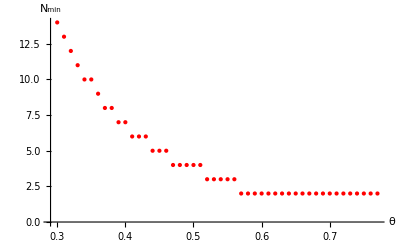

```mathematica
X=ListPlot[{{0.3,14},
{0.31,13},
{0.32,12},
{0.33,11},
{0.34,10},
{0.35000000000000003,10},
{0.36000000000000004,9},
{0.37000000000000005,8},
{0.38000000000000006,8},
{0.39000000000000007,7},
{0.4000000000000001,7},
{0.4100000000000001,6},
{0.4200000000000001,6},
{0.4300000000000001,6},
{0.4400000000000001,5},
{0.4500000000000001,5},
{0.46000000000000013,5},
{0.47000000000000014,4},
{0.48000000000000015,4},
{0.49000000000000016,4},
{0.5000000000000001,4},
{0.5100000000000001,4},
{0.5200000000000001,3},
{0.5300000000000001,3},
{0.5400000000000001,3},
{0.5500000000000002,3},
{0.5600000000000002,3},
{0.5700000000000002,2},
{0.5800000000000002,2},
{0.5900000000000002,2},
{0.6000000000000002,2},
{0.6100000000000002,2},
{0.6200000000000002,2},
{0.6300000000000002,2},
{0.6400000000000002,2},
{0.6500000000000002,2},
{0.6600000000000003,2},
{0.6700000000000003,2},
{0.6800000000000003,2},
{0.6900000000000003,2},
{0.7000000000000003,2},
{0.7100000000000003,2},
{0.7200000000000003,2},
{0.7300000000000003,2},
{0.7400000000000003,2},
{0.7500000000000003,2},
{0.7600000000000003,2},
{0.7700000000000004,2}},AxesLabel->{Style[θ,Black,Bold,15],Style[Subscript[N,min],Black,Bold,15]},AxesStyle->{{Bold,Black},{Bold,Black}},
TicksStyle->Directive[FontSize->13],PlotStyle->{PointSize->Large,Red}]
```

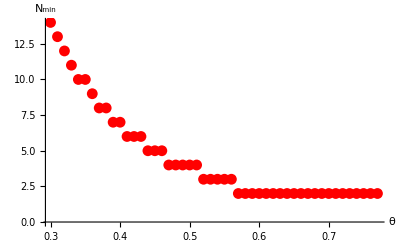

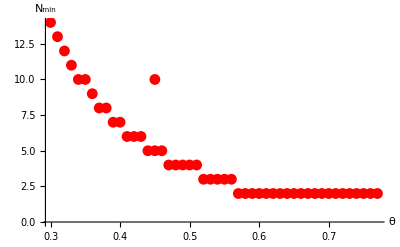

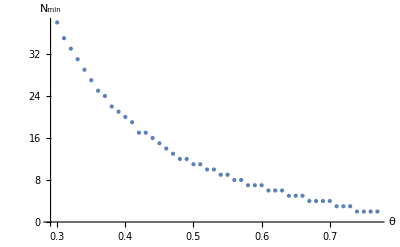

```mathematica
Y=ListPlot[{{0.3,38},
{0.31,35},
{0.32,33},
{0.33,31},
{0.34,29},
{0.35,27},
{0.36,25},
{0.37,24},
{0.38,22},
{0.39,21},
{0.40,20},
{0.41,19},
{0.42,17},
{0.43,17},
{0.44,16},
{0.45,15},
{0.46,14},
{0.47,13},
{0.48,12},
{0.49,12},
{0.50,11},
{0.51,11},
{0.52,10},
{0.53,10},
{0.54,9},
{0.55,9},
{0.56,8},
{0.57,8},
{0.58,7},
{0.59,7},
{0.60,7},
{0.61,6},
{0.62,6},
{0.63,6},
{0.64,5},
{0.65,5},
{0.66,5},
{0.67,4},
{0.68,4},
{0.69,4},
{0.70,4},
{0.71,3},
{0.72,3},
{0.73,3},
{0.74,2},{0.75,2},{0.76,2},{0.77,2}},AxesLabel->{Style[θ,Black,Bold,15],Style[Subscript[N,min],Black,Bold,15]},AxesStyle->{{Bold,Black},{Bold,Black}},
TicksStyle->Directive[FontSize->13],PlotStyle->{PointSize->Large}]
```

```mathematica
a
```

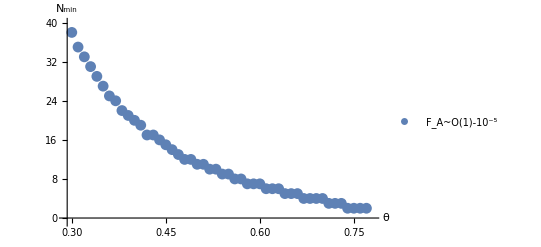

```mathematica
Show[Y,X]
```

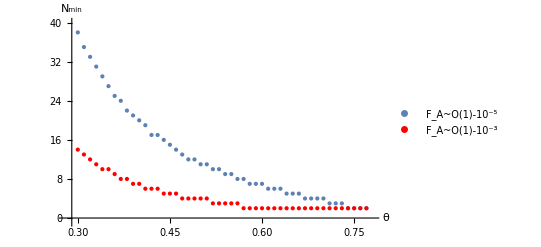

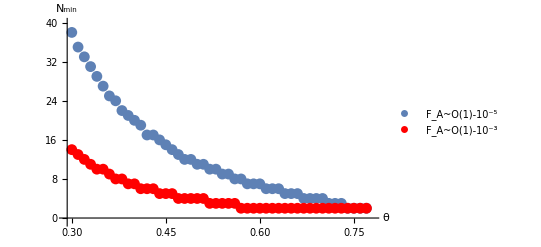

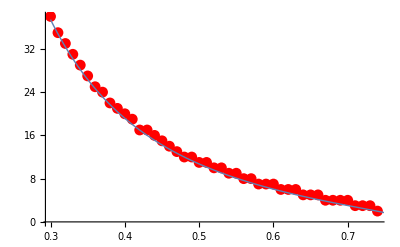

```mathematica
Show[ListPlot[{{0.3,38},
{0.31,35},
{0.32,33},
{0.33,31},
{0.34,29},
{0.35,27},
{0.36,25},
{0.37,24},
{0.38,22},
{0.39,21},
{0.40,20},
{0.41,19},
{0.42,17},
{0.43,17},
{0.44,16},
{0.45,15},
{0.46,14},
{0.47,13},
{0.48,12},
{0.49,12},
{0.50,11},
{0.51,11},
{0.52,10},
{0.53,10},
{0.54,9},
{0.55,9},
{0.56,8},
{0.57,8},
{0.58,7},
{0.59,7},
{0.60,7},
{0.61,6},
{0.62,6},
{0.63,6},
{0.64,5},
{0.65,5},
{0.66,5},
{0.67,4},
{0.68,4},
{0.69,4},
{0.70,4},
{0.71,3},
{0.72,3},
{0.73,3},
{0.74,2}},PlotStyle->Red],Plot[{-(1 Log[-1250.062503125294 (-2Sec[2θ]+2. Tan[2θ])])/Log[Cos[2θ]]},{θ,0.3,0.75},PlotStyle->{Thick},AxesLabel->{N,θ},AxesStyle->Thick]]
```

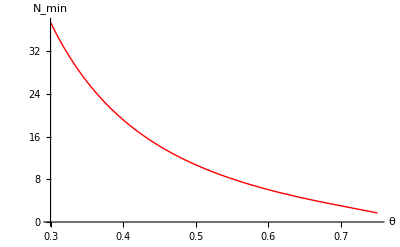

```mathematica
X=Plot[{-(1 Log[-1250.062503125294 (-2Sec[2θ]+2. Tan[2θ])])/Log[Cos[2θ]]},{θ,0.3,0.75},PlotStyle->{{Thick,Red}},AxesLabel->{θ,N_min},AxesStyle->Thick]
```

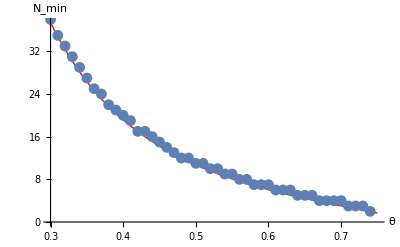

```mathematica
Show[X,Y]
```

```mathematica
data={{0.3,38},
{0.31,35},
{0.32,33},
{0.33,31},
{0.34,29},
{0.35,27},
{0.36,25},
{0.37,24},
{0.38,22},
{0.39,21},
{0.40,20},
{0.41,19},
{0.42,17},
{0.43,17},
{0.44,16},
{0.45,15},
{0.46,14},
{0.47,13},
{0.48,12},
{0.49,12},
{0.50,11},
{0.51,11},
{0.52,10},
{0.53,10},
{0.54,9},
{0.55,9},
{0.56,8},
{0.57,8},
{0.58,7},
{0.59,7},
{0.60,7},
{0.61,6},
{0.62,6},
{0.63,6},
{0.64,5},
{0.65,5},
{0.66,5},
{0.67,4},
{0.68,4},
{0.69,4},
{0.70,4},
{0.71,3},
{0.72,3},
{0.73,3},
{0.74,2},{0.75,2},{0.76,2},{0.77,2}};
```

```mathematica
line=Fit[data,{1,x},x]
```

47.6203-65.5287 x

```mathematica
quad=Fit[data,{1,x,x^2},x]
```

95.9583-259.219 x+181.019 x^2

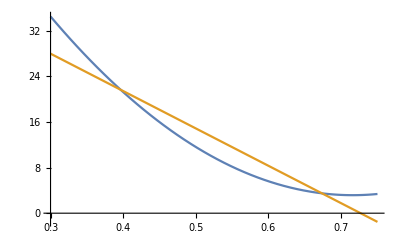

```mathematica
Plot[{95.95833624384072-259.21857595952366 x+181.01861466140613 x^2},{x,0.3,0.75}]
```

```mathematica
Assemblages in 2SDI
```

2 Assemblages in SDI

```mathematica
For[l=1,l<4,l++,
For[k=1,k<4,k++,
For[i=0,i<2,i++,
For[j=0,j<2,j++,
S[i,j,l,k]=Simplify[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,(σ[0]+(-1)^j σ[k])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,(σ[0]+(-1)^j σ[k])/2,σ[0]]]];
s[i,j,l,k]=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S[i,j,l,k].KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S[i,j,l,k].KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S[i,j,l,k].KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S[i,j,l,k].KroneckerProduct[d,d,σ[0]]];
Print[{i,j,l-1,k-1}];
Print[MatrixForm[s[i,j,l,k]]];
(*C0=Simplify[Tan[θ](u.ut)+d.dt];
C0T=Simplify[ConjugateTranspose[C0],{0<θ<π,0<Tan[θ]<1}];
K1=Simplify[√(1-Tan[θ]^2)(u.ut)];
K1T=Simplify[ConjugateTranspose[K1],{0<θ<π,0<Tan[θ]<1}];
sD[i,j,l,k]=Simplify[K0.s[i,j,l,k].K0T];
Print[MatrixForm[sD[i,j,l,k]]];*)
θ=π/4;
g[i,j,l,k]=s[i,j,l,k];
Clear[θ];
(*Pgf=Simplify[(1-(2 Sin[θ]^2))^(cp-1)];Pgs=Simplify[1-(1-(2 Sin[θ]^2))^(cp-1)];
gD[i,j,l,k]=Simplify[Pgs*g[i,j,l,k]+Pgf*s[i,j,l,k]];*)]]]]
Clear[l,i,j,k]
```

{0,0,0,0}

(1/8 (1+v Cos[2 θ]) | 1/4 v Cos[θ] Sin[θ]
1/4 v Cos[θ] Sin[θ] | 1/8 (1-v Cos[2 θ]))

{0,1,0,0}

(1/8 (1+v Cos[2 θ]) | -1/4 v Cos[θ] Sin[θ]
-1/4 v Cos[θ] Sin[θ] | 1/8 (1-v Cos[2 θ]))

{1,0,0,0}

(1/8 (1+v Cos[2 θ]) | -1/4 v Cos[θ] Sin[θ]
-1/4 v Cos[θ] Sin[θ] | 1/8 (1-v Cos[2 θ]))

{1,1,0,0}

(1/8 (1+v Cos[2 θ]) | 1/4 v Cos[θ] Sin[θ]
1/4 v Cos[θ] Sin[θ] | 1/8 (1-v Cos[2 θ]))

{0,0,0,1}

(1/8 (1+v Cos[2 θ]) | 1/4 ⅈ v Cos[θ] Sin[θ]
-1/4 ⅈ v Cos[θ] Sin[θ] | 1/8 (1-v Cos[2 θ]))

{0,1,0,1}

(1/8 (1+v Cos[2 θ]) | -1/4 ⅈ v Cos[θ] Sin[θ]
1/4 ⅈ v Cos[θ] Sin[θ] | 1/8 (1-v Cos[2 θ]))

{1,0,0,1}

(1/8 (1+v Cos[2 θ]) | -1/4 ⅈ v Cos[θ] Sin[θ]
1/4 ⅈ v Cos[θ] Sin[θ] | 1/8 (1-v Cos[2 θ]))

{1,1,0,1}

(1/8 (1+v Cos[2 θ]) | 1/4 ⅈ v Cos[θ] Sin[θ]
-1/4 ⅈ v Cos[θ] Sin[θ] | 1/8 (1-v Cos[2 θ]))

{0,0,0,2}

(1/8 (1+v+2 v Cos[2 θ]) | 0
0 | (1-v)/8)

{0,1,0,2}

((1-v)/8 | 0
0 | 1/8 (1+v-2 v Cos[2 θ]))

{1,0,0,2}

(1/8 (1+v+2 v Cos[2 θ]) | 0
0 | (1-v)/8)

{1,1,0,2}

((1-v)/8 | 0
0 | 1/8 (1+v-2 v Cos[2 θ]))

{0,0,1,0}

(1/8 (1+v Cos[2 θ]) | 1/4 ⅈ v Cos[θ] Sin[θ]
-1/4 ⅈ v Cos[θ] Sin[θ] | 1/8 (1-v Cos[2 θ]))

{0,1,1,0}

(1/8 (1+v Cos[2 θ]) | -1/4 ⅈ v Cos[θ] Sin[θ]
1/4 ⅈ v Cos[θ] Sin[θ] | 1/8 (1-v Cos[2 θ]))

{1,0,1,0}

(1/8 (1+v Cos[2 θ]) | -1/4 ⅈ v Cos[θ] Sin[θ]
1/4 ⅈ v Cos[θ] Sin[θ] | 1/8 (1-v Cos[2 θ]))

{1,1,1,0}

(1/8 (1+v Cos[2 θ]) | 1/4 ⅈ v Cos[θ] Sin[θ]
-1/4 ⅈ v Cos[θ] Sin[θ] | 1/8 (1-v Cos[2 θ]))

{0,0,1,1}

(1/8 (1+v Cos[2 θ]) | -1/4 v Cos[θ] Sin[θ]
-1/4 v Cos[θ] Sin[θ] | 1/8 (1-v Cos[2 θ]))

{0,1,1,1}

(1/8 (1+v Cos[2 θ]) | 1/4 v Cos[θ] Sin[θ]
1/4 v Cos[θ] Sin[θ] | 1/8 (1-v Cos[2 θ]))

{1,0,1,1}

(1/8 (1+v Cos[2 θ]) | 1/4 v Cos[θ] Sin[θ]
1/4 v Cos[θ] Sin[θ] | 1/8 (1-v Cos[2 θ]))

{1,1,1,1}

(1/8 (1+v Cos[2 θ]) | -1/4 v Cos[θ] Sin[θ]
-1/4 v Cos[θ] Sin[θ] | 1/8 (1-v Cos[2 θ]))

{0,0,1,2}

(1/8 (1+v+2 v Cos[2 θ]) | 0
0 | (1-v)/8)

{0,1,1,2}

((1-v)/8 | 0
0 | 1/8 (1+v-2 v Cos[2 θ]))

{1,0,1,2}

(1/8 (1+v+2 v Cos[2 θ]) | 0
0 | (1-v)/8)

{1,1,1,2}

((1-v)/8 | 0
0 | 1/8 (1+v-2 v Cos[2 θ]))

{0,0,2,0}

(1/8 (1+v+2 v Cos[2 θ]) | 0
0 | (1-v)/8)

{0,1,2,0}

(1/8 (1+v+2 v Cos[2 θ]) | 0
0 | (1-v)/8)

{1,0,2,0}

((1-v)/8 | 0
0 | 1/8 (1+v-2 v Cos[2 θ]))

{1,1,2,0}

((1-v)/8 | 0
0 | 1/8 (1+v-2 v Cos[2 θ]))

{0,0,2,1}

(1/8 (1+v+2 v Cos[2 θ]) | 0
0 | (1-v)/8)

{0,1,2,1}

(1/8 (1+v+2 v Cos[2 θ]) | 0
0 | (1-v)/8)

{1,0,2,1}

((1-v)/8 | 0
0 | 1/8 (1+v-2 v Cos[2 θ]))

{1,1,2,1}

((1-v)/8 | 0
0 | 1/8 (1+v-2 v Cos[2 θ]))

{0,0,2,2}

(1/8 (1+3 v+4 v Cos[2 θ]) | 0
0 | (1-v)/8)

{0,1,2,2}

((1-v)/8 | 0
0 | (1-v)/8)

{1,0,2,2}

((1-v)/8 | 0
0 | (1-v)/8)

{1,1,2,2}

((1-v)/8 | 0
0 | 1/8-v/8+v Sin[θ]^2)

```mathematica
Simplify[MatrixForm[KroneckerProduct[(σ[0]-(*(-1)^1*)σ[3])/2,(σ[0]+(*(-1)^1*)σ[3])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]-(*(-1)^1*)σ[3])/2,(σ[0]+(*(-1)^1*)σ[3])/2,σ[0]]]]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[s[1,1,3,1,0]]
```

(0 | 0
0 | Sin[θ]^2/2)

```mathematica
For[l=1,l<4,l++,
For[k=1,k<4,k++,
Fg2S[l,k]=Sum[√Tr[g[l,i,k,j,0].gD[l,i,k,j,0]],{i,0,1,1},{j,0,1,1}]]];
```

```mathematica
Simplify[Fg2S[3,2]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
Simplify[Fg2S[1,1]-Fg2S[3,2]]
```

1/2 (-√(1-Cos[2 θ]^cp)-√(1+Cos[2 θ]^cp)+√(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ])))

#### Local filtering operation by Bob and Charlie in 1SDI scenario

```mathematica
Strategy 1 (one party contribution)
```

contribution one party Strategy

```mathematica
K0=Simplify[Tan[θ](u.ut)+d.dt];
MatrixForm[K0]
K0T=Simplify[ConjugateTranspose[K0],{0<θ<π,0<Tan[θ]<1}];
MatrixForm[K0T]
K1=Simplify[√(1-Tan[θ]^2)(u.ut)];
MatrixForm[K1]
K1T=Simplify[ConjugateTranspose[K1],{0<θ<π,0<Tan[θ]<1}];
MatrixForm[K1T]
Simplify[K0T.K0+K1T.K1]
```

(Tan[θ] | 0
0 | 1)

(Tan[θ] | 0
0 | 1)

(√(1-Tan[θ]^2) | 0
0 | 0)

(√(1-Tan[θ]^2) | 0
0 | 0)

{{1,0},{0,1}}

```mathematica
Strategy 2 (Equal contribution)
```

2 contribution Equal Strategy

```mathematica
E0=Simplify[√Tan[θ](u.ut)+d.dt];
MatrixForm[E0]
E0T=Simplify[ConjugateTranspose[E0],{0<θ<π,0<Tan[θ]<1}];
MatrixForm[E0T]
E1=Simplify[√(1-Tan[θ])(u.ut)];
MatrixForm[E1]
E1T=Simplify[ConjugateTranspose[E1],{0<θ<π,0<Tan[θ]<1}];
MatrixForm[E1T]
Simplify[E0T.E0+E1T.E1]
```

(√Tan[θ] | 0
0 | 1)

(√Tan[θ] | 0
0 | 1)

(√(1-Tan[θ]) | 0
0 | 0)

(√(1-Tan[θ]) | 0
0 | 0)

{{1,0},{0,1}}

```mathematica
Strategy 3 (Unequal contribution)
```

3 contribution Strategy Unequal

```mathematica
F0=Simplify[(Tan[θ])^(1/n)(u.ut)+d.dt];
MatrixForm[F0]
F0T=Simplify[ConjugateTranspose[F0],{0<θ<π,0<Tan[θ]<1,0<n<500}];
MatrixForm[F0T]
F1=Simplify[√(1-(Tan[θ])^(2/n))(u.ut)];
MatrixForm[F1]
F1T=Simplify[ConjugateTranspose[F1],{(*0<θ<π,*)(*0<Tan[θ]<1,*)0<Tan[θ]^(2/n)<1}];
MatrixForm[F1T]
Simplify[F0T.F0+F1T.F1]
F2=Simplify[(Tan[θ])^((n-1)/n)(u.ut)+d.dt];
MatrixForm[F2]
F2T=Simplify[ConjugateTranspose[F2],{0<θ<π,0<Tan[θ]<1,0<n<500}];
MatrixForm[F2T]
F3=Simplify[√(1-(Tan[θ])^(2(n-1)/n))(u.ut)];
MatrixForm[F3]
F3T=Simplify[ConjugateTranspose[F3],{(*0<θ<π,*)(*0<Tan[θ]<1,*)0<Tan[θ]^(2/n)<1}];
MatrixForm[F3T]
Simplify[F2T.F2+F3T.F3]
```

(Tan[θ]^(1/n) | 0
0 | 1)

(Tan[θ]^(1/n) | 0
0 | 1)

(√(1-Tan[θ]^(2/n)) | 0
0 | 0)

(Conjugate[√(1-Tan[θ]^(2/n))] | 0
0 | 0)

{{Tan[θ]^(2/n)+Conjugate[√(1-Tan[θ]^(2/n))] √(1-Tan[θ]^(2/n)),0},{0,1}}

(Tan[θ]^((-1+n)/n) | 0
0 | 1)

(Tan[θ]^((-1+n)/n) | 0
0 | 1)

(√(1-Tan[θ]^(2-2/n)) | 0
0 | 0)

(Conjugate[√(1-Tan[θ]^(2-2/n))] | 0
0 | 0)

{{Tan[θ]^(2-2/n)+Conjugate[√(1-Tan[θ]^(2-2/n))] √(1-Tan[θ]^(2-2/n)),0},{0,1}}

```mathematica
Probability of getting outcome 0 in 1SDI
```

0

```mathematica
P11SGHZ=Simplify[Tr[KroneckerProduct[K0,σ[0]].(s[1,0,0,0]+s[1,1,0,0]).KroneckerProduct[K0T,σ[0]]]]
```

2 Sin[θ]^2

```mathematica
P21SGHZ=Simplify[Tr[KroneckerProduct[E0,E0].(s[2,0,0,0]+s[2,1,0,0]).KroneckerProduct[E0T,E0T]]]
```

2 Sin[θ]^2

```mathematica
P31SGHZ=Simplify[Tr[KroneckerProduct[F0,F2].(s[3,0,0,0]+s[3,1,0,0]).KroneckerProduct[F0T,F2T]](*+Tr[KroneckerProduct[F0,F2].(s101+s111).KroneckerProduct[F0T,F2T]]*)]
```

2 Sin[θ]^2

```mathematica
GHZ state after the action of filtering operation
```

action after filtering GHZ of operation state the

```mathematica
ρfs1g=Simplify[KroneckerProduct[σ[0],σ[0],K0].ρg.KroneckerProduct[σ[0],σ[0],K0T]];
MatrixForm[ρfs1g]
```

(Sin[θ]^2 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ]^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Sin[θ]^2 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ]^2)

```mathematica
ρfs2g=Simplify[KroneckerProduct[σ[0],E0,E0].ρg.KroneckerProduct[σ[0],E0T,E0T]];
MatrixForm[ρfs2g]
```

(Sin[θ]^2 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ]^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Sin[θ]^2 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ]^2)

```mathematica
ρfs3g=Simplify[KroneckerProduct[σ[0],F0,F2].ρg.KroneckerProduct[σ[0],F0T,F2T]];
MatrixForm[ρfs3g]
```

(Sin[θ]^2 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ]^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Sin[θ]^2 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ]^2)

```mathematica
ρfS3g=Simplify[KroneckerProduct[σ[0],F2,F0].ρg.KroneckerProduct[σ[0],F2T,F0T]];
MatrixForm[ρfS3g]
```

(Sin[θ]^2 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ]^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Sin[θ]^2 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ]^2)

```mathematica
Probability of getting outcome 0 in 2SDI
```

0

```mathematica
P12SGHZ=Simplify[Tr[K0.(s[1,0,1,0,0]+s[1,0,1,1,0]+s[1,1,1,0,0]+s[1,1,1,1,0]).K0T]]
P22SGHZ=Simplify[Tr[K0.(s[2,0,1,0,0]+s[2,0,1,1,0]+s[2,1,1,0,0]+s[2,1,1,1,0]).K0T]]
P32SGHZ=Simplify[Tr[K0.(s[3,0,1,0,0]+s[3,0,1,1,0]+s[3,1,1,0,0]+s[3,1,1,1,0]).K0T]]
P42SGHZ=Simplify[Tr[K0.(s[1,0,2,0,0]+s[1,0,2,1,0]+s[1,1,2,0,0]+s[1,1,2,1,0]).K0T]]
P52SGHZ=Simplify[Tr[K0.(s[1,0,3,0,0]+s[1,0,3,1,0]+s[1,1,3,0,0]+s[1,1,3,1,0]).K0T]]
P62SGHZ=Simplify[Tr[K0.(s[2,0,2,0,0]+s[2,0,2,1,0]+s[2,1,2,0,0]+s[2,1,2,1,0]).K0T]]
P72SGHZ=Simplify[Tr[K0.(s[3,0,2,0,0]+s[3,0,2,1,0]+s[3,1,2,0,0]+s[3,1,2,1,0]).K0T]]
P82SGHZ=Simplify[Tr[K0.(s[2,0,3,0,0]+s[2,0,3,1,0]+s[2,1,3,0,0]+s[2,1,3,1,0]).K0T]]
P92SGHZ=Simplify[Tr[K0.(s[3,0,3,0,0]+s[3,0,3,1,0]+s[3,1,3,0,0]+s[3,1,3,1,0]).K0T]]
```

2 Sin[θ]^2

2 Sin[θ]^2

2 Sin[θ]^2

«6 more identical outputs»

```mathematica
Failure probability
```

Failure probability

```mathematica
Pf11SGHZ=Simplify[Tr[KroneckerProduct[K1,σ[0]].(s[1,0,0,0]+s[1,1,0,0]).KroneckerProduct[K1T,σ[0]]]]
```

Cos[2 θ]

```mathematica
Pf21SGHZ=Simplify[Tr[KroneckerProduct[E1,E1].(s[1,0,0,0]+s[1,0,0,0]).KroneckerProduct[E1,E1]]+Tr[KroneckerProduct[E0,E1].(s[1,0,0,0]+s[1,0,0,0]).KroneckerProduct[E0,E1]]+Tr[KroneckerProduct[E1,E0].(s[1,0,0,0]+s[1,0,0,0]).KroneckerProduct[E1,E0]]]
```

Cos[2 θ]

```mathematica
Pf31SGHZ=Simplify[Tr[KroneckerProduct[F0,F1].(s101+s111).KroneckerProduct[F0,F1]]+Tr[KroneckerProduct[F0,F3].(s101+s111).KroneckerProduct[F0,F3]]+Tr[KroneckerProduct[F1,F0].(s101+s111).KroneckerProduct[F1,F0]]+
Tr[KroneckerProduct[F1,F2].(s101+s111).KroneckerProduct[F1,F2]]+Tr[KroneckerProduct[F1,F3].(s101+s111).KroneckerProduct[F1,F3]]+Tr[KroneckerProduct[F2,F1].(s101+s111).KroneckerProduct[F2,F1]]+Tr[KroneckerProduct[F2,F3].(s101+s111).KroneckerProduct[F2,F3]]+Tr[KroneckerProduct[F3,F0].(s101+s111).KroneckerProduct[F3,F0]]+Tr[KroneckerProduct[F3,F1].(s101+s111).KroneckerProduct[F3,F1]]+Tr[KroneckerProduct[F3,F2].(s101+s111).KroneckerProduct[F3,F2]]+
Tr[KroneckerProduct[F0,F0].(s101+s111).KroneckerProduct[F0,F0]]+Tr[KroneckerProduct[F3,F3].(s101+s111).KroneckerProduct[F3,F3]]+Tr[KroneckerProduct[F1,F1].(s101+s111).KroneckerProduct[F1,F1]]+Tr[KroneckerProduct[F2,F2].(s101+s111).KroneckerProduct[F2,F2]]]
```

```mathematica
Simplify[P11SGHZ+Pf11SGHZ]
```

1

```mathematica
Simplify[P21SGHZ+Pf21SGHZ]
```

1

```mathematica
Simplify[P31SGHZ+Pf31SGHZ]
```

#### Assemblage fidelity for finite copy 1SDI previous method

```mathematica
u00=({{1},{0},{0},{0}});
u01=({{0},{1},{0},{0}});
u10=({{0},{0},{1},{0}});
u11=({{0},{0},{0},{1}});
ut00=ConjugateTranspose[u00];
ut01=ConjugateTranspose[u01];
ut10=ConjugateTranspose[u10];
ut11=ConjugateTranspose[u11];
Pgf=Simplify[(1-(2 Sin[θ]^2))^(cp-1)];Pgs=Simplify[1-(1-(2 Sin[θ]^2))^(cp-1)];
```

```mathematica
Fg0=Simplify[√Tr[g[1,0,0,0].gD[1,0,0,0]]+√Tr[g[1,1,0,0].gD[1,1,0,0]]]
```

1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))

```mathematica
Fg1=Simplify[√Tr[g[2,0,0,0].gD[2,0,0,0]]+√Tr[g[2,1,0,0].gD[2,1,0,0]]]
```

(√(2+Cos[2 θ]^(-1+cp) (-1+Sin[2 θ])))/(√2)

```mathematica
Fg3=Simplify[√Tr[g[3,0,0,0].gD[3,0,0,0]]+√Tr[g[3,1,0,0].gD[3,1,0,0]]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
Fg1=Simplify[1/(√4)(√((ut00.gD101.u00)+(ut00.gD101.u11)+(ut11.gD101.u00)+(ut11.gD101.u11))+√((ut00.gD111.u00)-(ut00.gD111.u11)-(ut11.gD111.u00)+(ut11.gD111.u11)))]
```

{{1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))}}

```mathematica
Simplify[√Tr[g101.gD101]+√Tr[g111.gD111]]
```

1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))

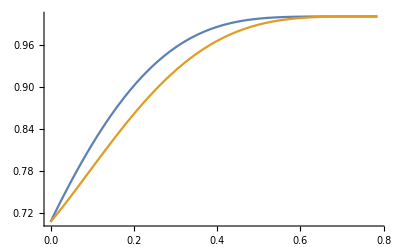

```mathematica
cp=3;
Plot[{1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp)),1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))(*,(√(2+Cos[2 θ]^(-1+cp) (-1+Sin[2 θ])))/(√2)*)},{θ,0,π/4}]
```

```mathematica
θ=0.25;cp=2;
Simplify[1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))-1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))]
Clear[θ,cp]
```

0.0265537

```mathematica
θ=0.2;cp=2;
Simplify[Fg0]//N
Simplify[Fg3]//N
Clear[θ,cp]
```

0.847826

0.87448

```mathematica
GHZ 1SDI
```

GHZ SDI

```mathematica
{{θ, cp=2, 5, 10, 50, 100, 380, □, □, □}, {0.1, 0.779308, 0.793939, 0.81593, 0.922288, 0.972324, 0.999903, □, □, □}, {0.2, cp=2, 5, 10, 50, 91, □, □, □, □}, {0.2, 0.847826, 0.88335, 0.924311, 0.997281, 0.999907, □, □, □, □}, {0.3, □, □, □, 20, 38, □, □, □, □}, {0.3, 0.905727, 0.948154, 0.980469, 0.99716, 0.99991, □, □, □, □}, {0.4, □, □, □, 20, □, □, □, □, □}, {0.4, 0.949495, 0.98321, 0.997263, 0.999926, □, □, □, □, □}, {0.5, □, □, 10, 11, □, □, □, □, □}, {0.5, 0.978352, 0.996617, 0.999844, 0.999916, □, □, □, □, □}, {0.6, □, □, 7, □, □, □, □, □, □}, {0.6, 0.993824, 0.999707, 0.999962, □, □, □, □, □, □}, {0.7, □, 4, □, □, □, □, □, □, □}, {0.7, 0.999382, 0.999982, □, □, □, □, □, □, □}, {0.8, □, □, □, □, □, □, □, □, □}, {0.8, 1, □, □, □, □, □, □, □, □}, {0.9, □, □, □, □, □, □, □, □, □}, {0.9, 0.999667, 4/0.99998, 1, □, □, □, □, □, □}}
{{1, 0.9962, 0.99932, 7/0.9998, □, □, □, □, □, □}, {1.1, 0.9844, 0.9942, 8/0.9999, □, □, □, □, □, □}, {1.2, 0.959, 0.975717, 12/0.9999, □, □, □, □, □, □}, {1.3, 0.9162, 0.932413, 0.994223, 24/0.9999, □, □, □, □, □}}
{{1.4, 0.854477, 0.85903, 0.957649, 60/0.9999, □, □, □, □, □}, {1.5, 0.774137, 0.766482, 0.84465, 0.947733, 0.982525, 356/0.9999, □, □, □}, {0.9, □, □, □, □, □, □, □, □, □}, {0.9, 0.999667, □, □, □, □, □, □, □, □}}
```

#### Assemblage fidelity for finite copy 2SDI

```mathematica
u00=({{1},{0},{0},{0}});
u01=({{0},{1},{0},{0}});
u10=({{0},{0},{1},{0}});
u11=({{0},{0},{0},{1}});
ut00=ConjugateTranspose[u00];
ut01=ConjugateTranspose[u01];
ut10=ConjugateTranspose[u10];
ut11=ConjugateTranspose[u11];
Pgf=Simplify[(1-(2 Sin[θ]^2))^(cp-1)];Pgs=Simplify[1-(1-(2 Sin[θ]^2))^(cp-1)];
```

```mathematica
For[l=1,l<4,l++,
For[k=1,k<4,k++,
Fg[l,k]=Sum[√Tr[g[l,i,k,j,0].gD[l,i,k,j,0]],{i,0,1,1},{j,0,1,1}]]];
```

```mathematica
Simplify[Fg[3,3]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
Fg21=Simplify[√Tr[g[1,0,1,0,0].gD[1,0,1,0,0]]+√Tr[g[1,0,1,1,0].gD[1,0,1,1,0]]+√Tr[g[1,1,1,0,0].gD[1,1,1,0,0]]+√Tr[g[1,1,1,1,0].gD[1,1,1,1,0]]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
4-partite GHZ state
```

4-GHZ partite state

#### Assemblages in 1SDI

```mathematica
1-sided DI for GGHZ state (n = 4)
```

1-4 DI for GGHZ sided state

```mathematica
For[l=1,l<4,l++,
For[i=0,i<2,i++,
S[l,i,0,0,0]=Simplify[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,σ[0],σ[0],σ[0]].ρg4.ConjugateTranspose[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,σ[0],σ[0],σ[0]]]];
s[l,i,0,0,0]=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0],σ[0]]].S[l,i,0,0,0].KroneckerProduct[u,σ[0],σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0],σ[0]]].S[l,i,0,0,0].KroneckerProduct[d,σ[0],σ[0],σ[0]]];
θ=π/4;
g[l,i,0,0,0]=s[l,i,0,0,0];
Clear[θ];
Pgf=Simplify[(1-(2 Sin[θ]^2))^(cp-1)];Pgs=Simplify[1-(1-(2 Sin[θ]^2))^(cp-1)];
gD[l,i,0,0,0]=Simplify[Pgs*g[l,i,0,0,0]+Pgf*s[l,i,0,0,0]];]];
Clear[l,q,r,i,j,k]
```

```mathematica
MatrixForm[g[2,1,0,0,0]]
```

(1/4 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4)

```mathematica
P41SGHZ=Simplify[Tr[KroneckerProduct[K0,σ[0],σ[0]].(s[1,0,0,0,0]+s[1,1,0,0,0]).KroneckerProduct[K0T,σ[0],σ[0]]]]
```

2 Sin[θ]^2

```mathematica
Simplify[Tr[KroneckerProduct[K0,σ[0],σ[0],σ[0]].(ρg4).KroneckerProduct[K0T,σ[0],σ[0],σ[0]]]]
```

2 Sin[θ]^2

```mathematica
L0=({{Tan[θ]^(1/q), 0}, {0, 1}});L1=({{Tan[θ]^(1/r), 0}, {0, 1}});L2=({{Tan[θ]^(1-1/q-1/r), 0}, {0, 1}});
```

```mathematica
MatrixForm[Simplify[KroneckerProduct[L0,L1,L2,σ[0]].(ρg4).KroneckerProduct[L0,L1,L2,σ[0]]]]
```

(Sin[θ]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ]^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Sin[θ]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ]^2)

```mathematica
Assemblage fideity
```

Assemblage fideity

```mathematica
For[l=1,l<4,l++,
For[i=0,i<2,i++,
Fg4[l]=Sum[√Tr[g[l,i,0,0,0].gD[l,i,0,0,0]],{i,0,1,1}]]]
```

```mathematica
Simplify[Fg4[3]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
2-sided DI for GGHZ state (n = 4)
```

2-4 DI for GGHZ sided state

```mathematica
For[l=1,l<4,l++,
For[k=1,k<4,k++,
For[i=0,i<2,i++,
For[j=0,j<2,j++,
(*For[k=0,k<2,k++,*)
(*For[l=0;l<2;l++,*)
S[l,i,k,j,0,0]=Simplify[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,(σ[0]+(-1)^j σ[k])/2,σ[0],σ[0]].ρg4.ConjugateTranspose[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,(σ[0]+(-1)^j σ[k])/2,σ[0],σ[0]]]];
s[l,i,k,j,0,0]=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0],σ[0]]].S[l,i,k,j,0,0].KroneckerProduct[u,u,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0],σ[0]]].S[l,i,k,j,0,0].KroneckerProduct[u,d,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0],σ[0]]].S[l,i,k,j,0,0].KroneckerProduct[d,u,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0],σ[0]]].S[l,i,k,j,0,0].KroneckerProduct[d,d,σ[0],σ[0]]];
θ=π/4;
g[l,i,k,j,0,0]=s[l,i,k,j,0,0];
Clear[θ];
Pgf=Simplify[(1-(2 Sin[θ]^2))^(cp-1)];Pgs=Simplify[1-(1-(2 Sin[θ]^2))^(cp-1)];
gD[l,i,k,j,0,0]=Simplify[Pgs*g[l,i,k,j,0,0]+Pgf*s[l,i,k,j,0,0]];]]]];
Clear[l,q,r,i,j,k]
```

```mathematica
MatrixForm[gD[1,1,1,1,0,0]]
```

(1/8 (1+Cos[2 θ]^cp) | 0 | 0 | 1/8 (1+Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/8 (1+Cos[2 θ]^(-1+cp) (-1+Sin[2 θ])) | 0 | 0 | 1/8 (1-Cos[2 θ]^cp))

```mathematica
Assemblage fideity
```

Assemblage fideity

```mathematica
For[l=1,l<4,l++,
For[k=1,k<4,k++,
Fg4[l,k]=Sum[√Tr[g[l,i,k,j,0,0].gD[l,i,k,j,0,0]],{i,0,1,1},{j,0,1,1}]]]
```

```mathematica
Simplify[Fg4[3,3]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
3-sided DI for GGHZ state (n = 4)
```

3-4 DI for GGHZ sided state

```mathematica
For[l=0,l<4,l++,
For[q=0,q<4,q++,
For[r=0,r<4,r++,
For[i=0,i<2,i++,
For[j=0,j<2,j++,
For[k=0,k<2,k++,
(*For[l=0;l<2;l++,*)
S[l,i,q,j,r,k,0]=Simplify[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,(σ[0]+(-1)^j σ[q])/2,(σ[0]+(-1)^k σ[r])/2,σ[0]].ρg4.ConjugateTranspose[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,(σ[0]+(-1)^j σ[q])/2,(σ[0]+(-1)^k σ[r])/2,σ[0]]]];
s[l,i,q,j,r,k,0]=Simplify[ConjugateTranspose[KroneckerProduct[u,u,u,σ[0]]].S[l,i,q,j,r,k,0].KroneckerProduct[u,u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,u,d,σ[0]]].S[l,i,q,j,r,k,0].KroneckerProduct[u,u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,u,σ[0]]].S[l,i,q,j,r,k,0].KroneckerProduct[u,d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,d,σ[0]]].S[l,i,q,j,r,k,0].KroneckerProduct[u,d,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,u,σ[0]]].S[l,i,q,j,r,k,0].KroneckerProduct[d,u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,d,σ[0]]].S[l,i,q,j,r,k,0].KroneckerProduct[d,u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,u,σ[0]]].S[l,i,q,j,r,k,0].KroneckerProduct[d,d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,d,σ[0]]].S[l,i,q,j,r,k,0].KroneckerProduct[d,d,d,σ[0]]];
θ=π/4;
g[l,i,q,j,r,k,0]=s[l,i,q,j,r,k,0];
Clear[θ];
Pgf=Simplify[(1-(2 Sin[θ]^2))^(cp-1)];Pgs=Simplify[1-(1-(2 Sin[θ]^2))^(cp-1)];
gD[l,i,q,j,r,k,0]=Simplify[Pgs*g[l,i,q,j,r,k,0]+Pgf*s[l,i,q,j,r,k,0]];]]]]]];
Clear[l,q,r,i,j,k]
```

```mathematica
MatrixForm[gD[1,1,1,1,1,0,0]]
```

(1/16 (1+Cos[2 θ]^cp) | 1/16 (1+Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))
1/16 (1+Cos[2 θ]^(-1+cp) (-1+Sin[2 θ])) | 1/16 (1-Cos[2 θ]^cp))

```mathematica
Assemblage fideity
```

Assemblage fideity

```mathematica
For[l=0,l<4,l++,
For[q=0,q<4,q++,
For[r=0,r<4,r++,
Fg4[l,q,r]=Sum[√Tr[g[l,i,q,j,r,k,0].gD[l,i,q,j,r,k,0]],{i,0,1,1},{j,0,1,1},{k,0,1,1}]]]]
```

```mathematica
Simplify[Fg4[3,1,3]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

#### W-state

#### Assemblages in 1SDI

```mathematica
For[l=1,l<4,l++,
For[i=0,i<2,i++,
Sw[i,l]=Simplify[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,σ[0],σ[0]].ρw.ConjugateTranspose[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,σ[0],σ[0]]]];
sw[i,l]=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0]]].Sw[i,l].KroneckerProduct[u,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0]]].Sw[i,l].KroneckerProduct[d,σ[0],σ[0]]];
Print[Simplify[Tr[Sw[i,l]]]];
Print[{i,l-1}];
Print[MatrixForm[sw[i,l]]];
c0=1/(√3);c1=1/(√3);c2=1/(√3);
gw[i,l]=sw[i,l];
Clear[c0,c1,c2];
Pgwf=Simplify[(1-((3 c0^2 c1^2)/c2^2))^(cp-1)];Pgws=Simplify[1-(1-((3 c0^2 c1^2)/c2^2))^(cp-1)];
gDw[i,l]=Simplify[Pgws*gw[i,l]+Pgwf*sw[i,l]];
]];
Clear[l,i,j,k]
```

1/2

{0,0}

(1/8 (1+(3-4 c0^2-4 c1^2) v) | 1/2 c0 √(1-c0^2-c1^2) v | 1/2 c1 √(1-c0^2-c1^2) v | 0
1/2 c0 √(1-c0^2-c1^2) v | 1/8 (1+(-1+4 c0^2) v) | (c0 c1 v)/2 | 0
1/2 c1 √(1-c0^2-c1^2) v | (c0 c1 v)/2 | 1/8 (1+(-1+4 c1^2) v) | 0
0 | 0 | 0 | (1-v)/8)

1/2

{1,0}

(1/8 (1+(3-4 c0^2-4 c1^2) v) | -1/2 c0 √(1-c0^2-c1^2) v | -1/2 c1 √(1-c0^2-c1^2) v | 0
-1/2 c0 √(1-c0^2-c1^2) v | 1/8 (1+(-1+4 c0^2) v) | (c0 c1 v)/2 | 0
-1/2 c1 √(1-c0^2-c1^2) v | (c0 c1 v)/2 | 1/8 (1+(-1+4 c1^2) v) | 0
0 | 0 | 0 | (1-v)/8)

1/2

{0,1}

(1/8 (1+(3-4 c0^2-4 c1^2) v) | -1/2 ⅈ c0 √(1-c0^2-c1^2) v | -1/2 ⅈ c1 √(1-c0^2-c1^2) v | 0
1/2 ⅈ c0 √(1-c0^2-c1^2) v | 1/8 (1+(-1+4 c0^2) v) | (c0 c1 v)/2 | 0
1/2 ⅈ c1 √(1-c0^2-c1^2) v | (c0 c1 v)/2 | 1/8 (1+(-1+4 c1^2) v) | 0
0 | 0 | 0 | (1-v)/8)

1/2

{1,1}

(1/8 (1+(3-4 c0^2-4 c1^2) v) | 1/2 ⅈ c0 √(1-c0^2-c1^2) v | 1/2 ⅈ c1 √(1-c0^2-c1^2) v | 0
-1/2 ⅈ c0 √(1-c0^2-c1^2) v | 1/8 (1+(-1+4 c0^2) v) | (c0 c1 v)/2 | 0
-1/2 ⅈ c1 √(1-c0^2-c1^2) v | (c0 c1 v)/2 | 1/8 (1+(-1+4 c1^2) v) | 0
0 | 0 | 0 | (1-v)/8)

1/2+(-1/2+c0^2+c1^2) v

{0,2}

((1-v)/8 | 0 | 0 | 0
0 | 1/8+(-1/8+c0^2) v | c0 c1 v | 0
0 | c0 c1 v | 1/8+(-1/8+c1^2) v | 0
0 | 0 | 0 | (1-v)/8)

1/2 (1+v-2 c0^2 v-2 c1^2 v)

{1,2}

(1/8 (1+(7-8 c0^2-8 c1^2) v) | 0 | 0 | 0
0 | (1-v)/8 | 0 | 0
0 | 0 | (1-v)/8 | 0
0 | 0 | 0 | (1-v)/8)

```mathematica
c0=1/√3;c1=1/√3;
Simplify[Eigenvalues[({{1/8 (1+(3-4 c0^2-4 c1^2) v), 1/2 c0 √(1-c0^2-c1^2) v, 1/2 c1 √(1-c0^2-c1^2) v, (c0 c1 v)/2}, {1/2 c0 √(1-c0^2-c1^2) v, 1/8 (1+(-1+4 c0^2) v), 0, 0}, {1/2 c1 √(1-c0^2-c1^2) v, 0, 1/8 (1+(-1+4 c1^2) v), 0}, {(c0 c1 v)/2, 0, 0, (1-v)/8}})/(1/2)],{0<c0<1,0<c1<1,0<v<1}]
Clear[c0,c1]
```

{1/12 (3-7 v),(3+v)/12,1/12 (3+(3-2 √5) v),1/12 (3+(3+2 √5) v)}

```mathematica
Reduce[1/12 (3-7 v)<0&&0<c0<1/√3&&0<c1<1/√3&&0<v<1,{v}]//N
```

0.<c0<0.57735&&0.<c1<0.57735&&0.428571<v<1.

```mathematica
c0=1/√3;c1=1/√3;
Simplify[Eigenvalues[({{(1-v)/8, 0, 0, c0 c1 v}, {0, 1/8+(-1/8+c0^2) v, 0, 0}, {0, 0, 1/8+(-1/8+c1^2) v, 0}, {c0 c1 v, 0, 0, (1-v)/8}})],{0<c0<1,0<c1<1,0<v<1}]
Clear[c0,c1]
```

{1/24 (3-11 v),1/24 (3+5 v),1/24 (3+5 v),1/24 (3+5 v)}

```mathematica
Reduce[1/24 (3-11 v)<0&&0<c0<1/√3&&0<c1<1/√3&&0<v<1,{v}]//N
```

0.<c0<0.57735&&0.<c1<0.57735&&0.272727<v<1.

```mathematica
a=Simplify[-I c0 KroneckerProduct[u,d]-I c1 KroneckerProduct[d,u]+ c2 KroneckerProduct[u,u]];
aT=Simplify[ConjugateTranspose[a],{0<c0<1,0<c1<1,0<c2<1}];
MatrixForm[a.aT]
```

(0 | 0 | 0 | 0
0 | c0^2 | c0 c1 | 0
0 | c0 c1 | c1^2 | 0
0 | 0 | 0 | 0)

```mathematica
MatrixForm[sw[3,0,0,0]]
```

(0 | 0 | 0 | 0
0 | c0^2 | c0 c1 | 0
0 | c0 c1 | c1^2 | 0
0 | 0 | 0 | 0)

```mathematica
$Assumptions = {0<c1<1/(√3),0<c0<1/(√3)};
(*c2 = √(1-c0^2-c1^2);*)
For[l=1,l<4,l++,
Fw[l]=Sum[√Tr[gw[l,i,0,0].gDw[l,i,0,0]],{i,0,1,1}]]
Simplify[1-(3 c0^2 c1^2)/c2^2]
FullSimplify[Fw[1]]
FullSimplify[Fw[3]]
Clear[c2]
```

1-(3 c0^2 c1^2)/c2^2

(√(3+((1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (-3+(c0+c1+c2)^2))/(-3 c0^2 c1^2+c2^2)))/(√3)

1/3 (√(1-(1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+3 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp) c2^2)+√(4-((-4+3 (c0+c1)^2) (1-(3 c0^2 c1^2)/c2^2)^cp c2^2)/(3 c0^2 c1^2-c2^2)))

```mathematica
(√(3+((X)^N c2^2 (-3+(c0+c1+c2)^2))/(-3 c0^2 c1^2+c2^2)))/(√3)
```

```mathematica
1/3 (√(1-(X)^(N-1)+3 (X)^(N-1) c2^2)+√(4-((-4+3 (c0+c1)^2) (X)^N c2^2)/(3 c0^2 c1^2-c2^2)))
```

```mathematica
cp=2;
Plot3D[{1/(√3)(√(1/(-1+c1^2+c0^2 (1+3 c1^2))(2 c0^3 (c1+√(1-c0^2-c1^2)) (1+(3 c0^2 c1^2)/(-1+c0^2+c1^2))^cp+2 c0 (-1+c1^2) (c1+√(1-c0^2-c1^2)) (1+(3 c0^2 c1^2)/(-1+c0^2+c1^2))^cp+(-1+c1^2) (3-2 (1+(3 c0^2 c1^2)/(-1+c0^2+c1^2))^cp+2 c1 √(1-c0^2-c1^2) (1+(3 c0^2 c1^2)/(-1+c0^2+c1^2))^cp)+c0^2 (3+9 c1^2-2 (1+(3 c0^2 c1^2)/(-1+c0^2+c1^2))^cp+2 c1 √(1-c0^2-c1^2) (1+(3 c0^2 c1^2)/(-1+c0^2+c1^2))^cp))))(*,√(1/9-((-1+c0^2+c1^2) (-2+3 c0^2+3 c1^2) (1+(3 c0^2 c1^2)/(-1+c0^2+c1^2))^cp)/(9 (-1+c1^2+c0^2 (1+3 c1^2))))+1/3 √(4+((-1+c0^2+c1^2) (-4+3 (c0+c1)^2) (1+(3 c0^2 c1^2)/(-1+c0^2+c1^2))^cp)/(-1+c1^2+c0^2 (1+3 c1^2)))*)},{c0,0,1/(√3)},{c1,0,1/(√3)},PlotStyle->{Red(*,Black*)},AxesLabel->{Subscript[c,0],Subscript[c,1],Superscript[Subscript[A,f],w]},AxesEdge->{{0,1/√3},{0,1/(√3)},{0.85,1}}]
Clear[cp]
```

-Graphics3D-

```mathematica
N_min data for 1SDI w-state
```

```mathematica
c2=√(1-c0^2-c1^2);c0=0.15;
For[c1=0.1,c1<1/√3,c1+=0.01,
	For[cp=2,cp<20000,cp++,
If[(√(3+((1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (-3+(c0+c1+c2)^2))/(-3 c0^2 c1^2+c2^2)))/(√3)>0.9999,Break[]]]Print[{c1,cp}]]
Clear[c0,c1,c2,cp]
```

{0.1,11191}

{0.11,9211}

{0.12,7706}

{0.13,6535}

{0.14,5608}

{0.15,4860}

{0.16,4248}

{0.17,3742}

{0.18,3318}

{0.19,2960}

{0.2,2654}

{0.21,2392}

{0.22,2164}

{0.23,1966}

{0.24,1792}

{0.25,1639}

{0.26,1503}

{0.27,1382}

{0.28,1274}

{0.29,1178}

{0.3,1090}

{0.31,1012}

{0.32,940}

{0.33,875}

{0.34,816}

{0.35,762}

{0.36,712}

{0.37,667}

{0.38,625}

{0.39,586}

{0.4,550}

{0.41,517}

{0.42,486}

{0.43,458}

{0.44,431}

{0.45,406}

{0.46,383}

{0.47,362}

{0.48,342}

{0.49,323}

{0.5,305}

{0.51,288}

{0.52,272}

{0.53,258}

{0.54,244}

{0.55,231}

{0.56,218}

{0.57,207}

```mathematica
c2=√(1-c0^2-c1^2);c0=0.15;
For[c1=0.1,c1<1/√3,c1+=0.01,
	For[cp=2,cp<20000,cp++,
If[(√(3+((1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (-3+(c0+c1+c2)^2))/(-3 c0^2 c1^2+c2^2)))/(√3)>0.9,Break[]]]Print[{c1,cp}]]
```

{0.57,7}

{0.56,8}

{0.55,10}

{0.54,11}

{0.53,13}

{0.52,15}

{0.51,17}

{0.5,18}

{0.49,20}

{0.48,22}

{0.47,25}

{0.46,27}

{0.45,29}

{0.44,32}

{0.43,35}

{0.42,38}

{0.41,41}

{0.4,44}

{0.39,48}

{0.38,52}

{0.37,56}

{0.36,61}

{0.35,65}

{0.34,71}

{0.33,77}

{0.32,83}

{0.31,91}

{0.3,99}

{0.29,107}

{0.28,117}

{0.27,128}

{0.26,140}

{0.25,154}

{0.24,169}

{0.23,187}

{0.22,207}

{0.21,230}

{0.2,257}

{0.19,288}

{0.18,325}

{0.17,368}

{0.16,421}

{0.15,484}

{0.14,561}

{0.13,657}

{0.12,779}

{0.11,936}

{0.1,1142}

{0.57,207}

{0.56,218}

{0.55,231}

{0.54,244}

{0.53,258}

{0.52,272}

{0.51,288}

{0.5,305}

{0.49,323}

{0.48,342}

{0.47,362}

{0.46,383}

{0.45,406}

{0.44,431}

{0.43,458}

{0.42,486}

{0.41,517}

{0.4,550}

{0.39,586}

{0.38,625}

{0.37,667}

{0.36,712}

{0.35,762}

{0.34,816}

{0.33,875}

{0.32,940}

{0.31,1012}

{0.3,1090}

{0.29,1178}

{0.28,1274}

{0.27,1382}

{0.26,1503}

{0.25,1639}

{0.24,1792}

{0.23,1966}

{0.22,2164}

{0.21,2392}

{0.2,2654}

{0.19,2960}

{0.18,3318}

{0.17,3742}

{0.16,4248}

{0.15,4860}

{0.14,5608}

{0.13,6535}

{0.12,7706}

{0.11,9211}

{0.1,11191}

{0.57,7}
{0.56,8}
{0.55,10}
{0.54,11}
{0.53,13}
{0.52,15}
{0.51,17}
{0.5,18}
{0.49,20}
{0.48,22}
{0.47,25}
{0.46,27}
{0.45,29}
{0.44,32}
{0.43,35}
{0.42,38}
{0.41,41}
{0.4,44}
{0.39,48}
{0.38,52}
{0.37,56}
{0.36,61}
{0.35,65}
{0.34,71}
{0.33,77}
{0.32,83}
{0.31,91}
{0.3,99}
{0.29,107}
{0.28,117}
{0.27,128}
{0.26,140}
{0.25,154}
{0.24,169}
{0.23,187}
{0.22,207}
{0.21,230}
{0.2,257}
{0.19,288}
{0.18,325}
{0.17,368}
{0.16,421}
{0.15,484}
{0.14,561}
{0.13,657}
{0.12,779}
{0.11,936}
{0.1,1142}

{0.57,72}
{0.56,76}
{0.55,81}
{0.54,86}
{0.53,91}
{0.52,97}
{0.51,102}
{0.5,109}
{0.49,116}
{0.48,123}
{0.47,131}
{0.46,139}
{0.45,148}
{0.44,158}
{0.43,168}
{0.42,179}
{0.41,191}
{0.4,204}
{0.39,218}
{0.38,234}
{0.37,250}
{0.36,269}
{0.35,288}
{0.34,310}
{0.33,334}
{0.32,360}
{0.31,389}
{0.3,421}
{0.29,456}
{0.28,495}
{0.27,539}
{0.26,588}
{0.25,643}
{0.24,706}
{0.23,777}
{0.22,858}
{0.21,952}
{0.2,1059}
{0.19,1185}
{0.18,1333}
{0.17,1508}
{0.16,1717}
{0.15,1970}
{0.14,2279}
{0.13,2664}
{0.12,3150}
{0.11,3775}
{0.1,4600}

{0.1,1367}
{0.11,1110}
{0.12,915}
{0.13,765}
{0.14,647}
{0.15,552}
{0.16,475}
{0.17,412}
{0.18,359}
{0.19,315}
{0.2,277}
{0.21,245}
{0.22,218}
{0.23,194}
{0.24,173}
{0.25,155}
{0.26,139}
{0.27,125}
{0.28,113}
{0.29,102}
{0.3,92}
{0.31,83}
{0.32,75}
{0.33,68}
{0.34,62}
{0.35,56}
{0.36,51}
{0.37,46}
{0.38,42}
{0.39,38}
{0.4,35}
{0.41,31}
{0.42,28}
{0.43,26}
{0.44,23}
{0.45,21}
{0.46,19}
{0.47,17}
{0.48,16}
{0.49,14}
{0.5,13}
{0.51,11}
{0.52,10}
{0.53,9}
{0.54,8}
{0.55,7}
{0.56,7}
{0.57,6}

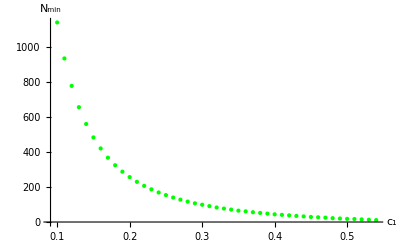

```mathematica
Zw15 =ListPlot[{(*{0.5700000000000004,7}
{0.5600000000000004,8},
{0.5500000000000004,10},*)
{0.5400000000000004,11},
{0.5300000000000004,13},
{0.5200000000000004,15},
{0.5100000000000003,17},
{0.5000000000000003,18},
{0.4900000000000003,20},
{0.4800000000000003,22},
{0.4700000000000003,25},
{0.4600000000000003,27},
{0.4500000000000003,29},
{0.4400000000000003,32},
{0.43000000000000027,35},
{0.42000000000000026,38},
{0.41000000000000025,41},
{0.40000000000000024,44},
{0.39000000000000024,48},
{0.3800000000000002,52},
{0.3700000000000002,56},
{0.3600000000000002,61},
{0.3500000000000002,65},
{0.3400000000000002,71},
{0.3300000000000002,77},
{0.3200000000000002,83},
{0.31000000000000016,91},
{0.30000000000000016,99},
{0.29000000000000015,107},
{0.28000000000000014,117},
{0.27000000000000013,128},
{0.2600000000000001,140},
{0.2500000000000001,154},
{0.2400000000000001,169},
{0.2300000000000001,187},
{0.22000000000000008,207},
{0.21000000000000008,230},
{0.20000000000000007,257},
{0.19000000000000006,288},
{0.18000000000000005,325},
{0.17000000000000004,368},
{0.16000000000000003,421},
{0.15000000000000002,484},
{0.14,561},
{0.13,657},
{0.12,779},
{0.11,936},
{0.1,1142}},AxesLabel->{Style[Subscript[c,1],Black,Bold,15],Style[Subscript[N,min],Black,Bold,15]},AxesStyle->{{Bold,Black},{Bold,Black}},
TicksStyle->Directive[FontSize->13],PlotStyle->{PointSize->Large,Green}]
```

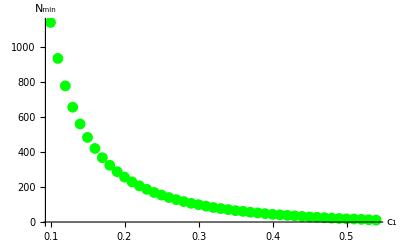

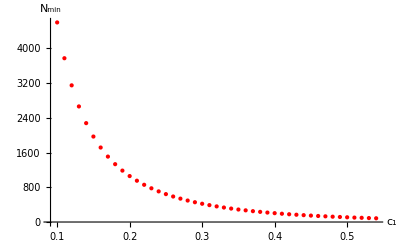

```mathematica
Yw15 =ListPlot[{(*{0.5700000000000004,72}
{0.5600000000000004,76},
{0.5500000000000004,81},*)
{0.5400000000000004,86},
{0.5300000000000004,91},
{0.5200000000000004,97},
{0.5100000000000003,102},
{0.5000000000000003,109},
{0.4900000000000003,116},
{0.4800000000000003,123},
{0.4700000000000003,131},
{0.4600000000000003,139},
{0.4500000000000003,148},
{0.4400000000000003,158},
{0.43000000000000027,168},
{0.42000000000000026,179},
{0.41000000000000025,191},
{0.40000000000000024,204},
{0.39000000000000024,218},
{0.3800000000000002,234},
{0.3700000000000002,250},
{0.3600000000000002,269},
{0.3500000000000002,288},
{0.3400000000000002,310},
{0.3300000000000002,334},
{0.3200000000000002,360},
{0.31000000000000016,389},
{0.30000000000000016,421},
{0.29000000000000015,456},
{0.28000000000000014,495},
{0.27000000000000013,539},
{0.2600000000000001,588},
{0.2500000000000001,643},
{0.2400000000000001,706},
{0.2300000000000001,777},
{0.22000000000000008,858},
{0.21000000000000008,952},
{0.20000000000000007,1059},
{0.19000000000000006,1185},
{0.18000000000000005,1333},
{0.17000000000000004,1508},
{0.16000000000000003,1717},
{0.15000000000000002,1970},
{0.14,2279},
{0.13,2664},
{0.12,3150},
{0.11,3775},
{0.1,4600}},AxesLabel->{Style[Subscript[c,1],Black,Bold,15],Style[Subscript[N,min],Black,Bold,15]},AxesStyle->{{Bold,Black},{Bold,Black}},
TicksStyle->Directive[FontSize->13],PlotStyle->{PointSize->Large,Red}]
```

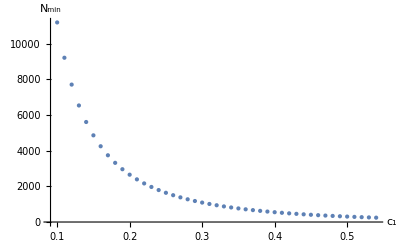

```mathematica
Xw15 =ListPlot[{{0.1,11191},{0.11,9211},{0.12,7706},{0.13,6535},{0.14,5608},{0.15,4860},{0.16,4248},{0.17,3742},{0.18,3318},
{0.19,2960},
{0.20,2654},
{0.21,2392},
{0.22,2164},
{0.23,1966},
{0.24,1792},
{0.25,1639},
{0.26,1503},
{0.27,1382},
{0.28,1274},
{0.29,1178},
{0.30,1090},
{0.31,1012},
{0.32,940},
{0.33,875},
{0.34,816},
{0.35,762},
{0.36,712},
{0.37,667},
{0.38,625},
{0.39,586},
{0.40,550},
{0.41,517},
{0.42,486},
{0.43,458},
{0.44,431},
{0.45,406},
{0.46,383},
{0.47,362},
{0.48,342},
{0.49,323},
{0.50,305},
{0.51,288},
{0.52,272},
{0.53,258},
{0.54,244}(*,
{0.55,231},
{0.56,218},
{0.57,207}*)},AxesLabel->{Style[Subscript[c,1],Black,Bold,15],Style[Subscript[N,min],Black,Bold,15]},AxesStyle->{{Bold,Black},{Bold,Black}},
TicksStyle->Directive[FontSize->13],PlotStyle->{PointSize->Large}]
```

```mathematica
Show[Xw15,Yw15,Zw15]
```

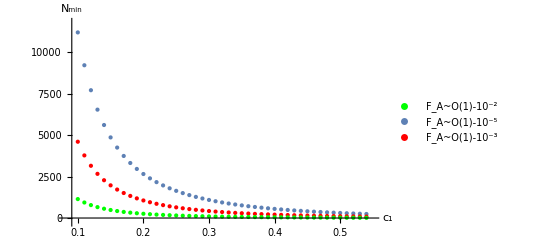

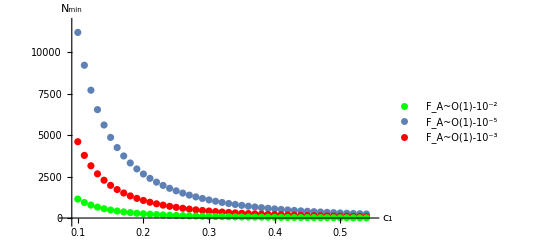

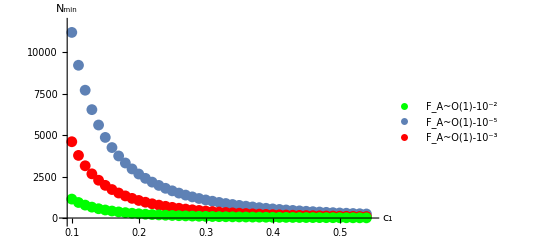

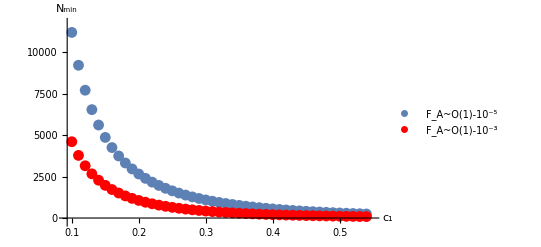

```mathematica
c2=√(1-c0^2-c1^2);c0=0.3;
For[c1=0.1,c1<1/√3,c1+=0.01,
	For[cp=2,cp<20000,cp++,
If[(√(3+((1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (-3+(c0+c1+c2)^2))/(-3 c0^2 c1^2+c2^2)))/(√3)>0.9999,Break[]]]Print[{c1,cp}]]
Clear[c0,c1,c2,cp]
```

{0.1,2526}
{0.11,2077}
{0.12,1735}
{0.13,1470}
{0.14,1260}
{0.15,1090}
{0.16,952}
{0.17,837}
{0.18,741}
{0.19,660}
{0.2,591}
{0.21,532}
{0.22,480}
{0.23,435}
{0.24,396}
{0.25,362}
{0.26,331}
{0.27,304}
{0.28,279}
{0.29,257}
{0.3,238}
{0.31,220}
{0.32,204}
{0.33,189}
{0.34,176}
{0.35,164}
{0.36,153}
{0.37,142}
{0.38,133}
{0.39,124}
{0.4,116}
{0.41,109}
{0.42,102}
{0.43,96}
{0.44,90}
{0.45,84}
{0.46,79}
{0.47,74}
{0.48,70}
{0.49,66}
{0.5,62}
{0.51,58}
{0.52,55}
{0.53,51}
{0.54,48}
{0.55,46}
{0.56,43}
{0.57,40}

```mathematica
c2=√(1-c0^2-c1^2);c0=0.3;
For[c1=0.1,c1<1/√3,c1+=0.01,
	For[cp=2,cp<20000,cp++,
If[(√(3+((1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (-3+(c0+c1+c2)^2))/(-3 c0^2 c1^2+c2^2)))/(√3)>0.99,Break[]]]Print[{c1,cp}]]
Clear[c0,c1,c2,cp]
```

{0.1,774}
{0.11,637}
{0.12,533}
{0.13,451}
{0.14,387}
{0.15,336}
{0.16,293}
{0.17,258}
{0.18,229}
{0.19,204}
{0.2,183}
{0.21,165}
{0.22,149}
{0.23,136}
{0.24,124}
{0.25,113}
{0.26,104}
{0.27,96}
{0.28,88}
{0.29,81}
{0.3,75}
{0.31,70}
{0.32,65}
{0.33,61}
{0.34,56}
{0.35,53}
{0.36,49}
{0.37,46}
{0.38,43}
{0.39,40}
{0.4,38}
{0.41,35}
{0.42,33}
{0.43,31}
{0.44,29}
{0.45,27}
{0.46,26}
{0.47,24}
{0.48,22}
{0.49,21}
{0.5,19}
{0.51,18}
{0.52,17}
{0.53,15}
{0.54,14}
{0.55,13}
{0.56,11}
{0.57,10}

```mathematica
c2=√(1-c0^2-c1^2);c0=0.3;
For[c1=0.1,c1<1/√3,c1+=0.01,
	For[cp=2,cp<20000,cp++,
If[(√(3+((1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (-3+(c0+c1+c2)^2))/(-3 c0^2 c1^2+c2^2)))/(√3)>0.9,Break[]]]Print[{c1,cp}]]
Clear[c0,c1,c2,cp]
```

{0.1,240}
{0.11,195}
{0.12,162}
{0.13,136}
{0.14,115}
{0.15,99}
{0.16,85}
{0.17,74}
{0.18,65}
{0.19,57}
{0.2,50}
{0.21,45}
{0.22,40}
{0.23,36}
{0.24,32}
{0.25,29}
{0.26,26}
{0.27,23}
{0.28,21}
{0.29,19}
{0.3,17}
{0.31,15}
{0.32,14}
{0.33,12}
{0.34,11}
{0.35,10}
{0.36,9}
{0.37,8}
{0.38,7}
{0.39,6}
{0.4,5}
{0.41,5}
{0.42,4}
{0.43,3}
{0.44,3}
{0.45,2}
{0.46,2}
{0.47,2}
{0.48,2}
{0.49,2}
{0.5,2}
{0.51,2}
{0.52,2}
{0.53,2}
{0.54,2}
{0.55,2}
{0.56,2}
{0.57,2}

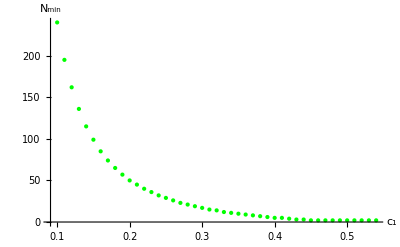

```mathematica
Zw3 = ListPlot[{{0.1,240},
{0.11,195},
{0.12,162},
{0.13,136},
{0.14,115},
{0.15000000000000002,99},
{0.16000000000000003,85},
{0.17000000000000004,74},
{0.18000000000000005,65},
{0.19000000000000006,57},
{0.20000000000000007,50},
{0.21000000000000008,45},
{0.22000000000000008,40},
{0.2300000000000001,36},
{0.2400000000000001,32},
{0.2500000000000001,29},
{0.2600000000000001,26},
{0.27000000000000013,23},
{0.28000000000000014,21},
{0.29000000000000015,19},
{0.30000000000000016,17},
{0.31000000000000016,15},
{0.3200000000000002,14},
{0.3300000000000002,12},
{0.3400000000000002,11},
{0.3500000000000002,10},
{0.3600000000000002,9},
{0.3700000000000002,8},
{0.3800000000000002,7},
{0.39000000000000024,6},
{0.40000000000000024,5},
{0.41000000000000025,5},
{0.42000000000000026,4},
{0.43000000000000027,3},
{0.4400000000000003,3},
{0.4500000000000003,2},
{0.4600000000000003,2},
{0.4700000000000003,2},
{0.4800000000000003,2},
{0.4900000000000003,2},
{0.5000000000000003,2},
{0.5100000000000003,2},
{0.5200000000000004,2},
{0.5300000000000004,2},
{0.5400000000000004,2}(*
{0.5500000000000004,2}
{0.5600000000000004,2}
{0.5700000000000004,2}*)},AxesLabel->{Style[Subscript[c,1],Black,Bold,15],Style[Subscript[N,min],Black,Bold,15]},AxesStyle->{{Bold,Black},{Bold,Black}},
TicksStyle->Directive[FontSize->13],PlotStyle->{PointSize->Large,Green}]
```

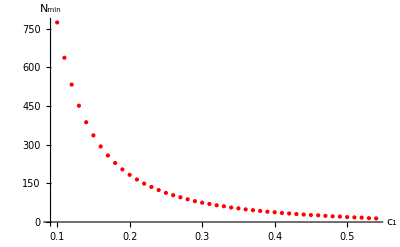

```mathematica
Xw3 = ListPlot[{{0.1,774},
{0.11,637},
{0.12,533},
{0.13,451},
{0.14,387},
{0.15000000000000002,336},
{0.16000000000000003,293},
{0.17000000000000004,258},
{0.18000000000000005,229},
{0.19000000000000006,204},
{0.20000000000000007,183},
{0.21000000000000008,165},
{0.22000000000000008,149},
{0.2300000000000001,136},
{0.2400000000000001,124},
{0.2500000000000001,113},
{0.2600000000000001,104},
{0.27000000000000013,96},
{0.28000000000000014,88},
{0.29000000000000015,81},
{0.30000000000000016,75},
{0.31000000000000016,70},
{0.3200000000000002,65},
{0.3300000000000002,61},
{0.3400000000000002,56},
{0.3500000000000002,53},
{0.3600000000000002,49},
{0.3700000000000002,46},
{0.3800000000000002,43},
{0.39000000000000024,40},
{0.40000000000000024,38},
{0.41000000000000025,35},
{0.42000000000000026,33},
{0.43000000000000027,31},
{0.4400000000000003,29},
{0.4500000000000003,27},
{0.4600000000000003,26},
{0.4700000000000003,24},
{0.4800000000000003,22},
{0.4900000000000003,21},
{0.5000000000000003,19},
{0.5100000000000003,18},
{0.5200000000000004,17},
{0.5300000000000004,15},
{0.5400000000000004,14}(*,
{0.5500000000000004,13},
{0.5600000000000004,11},
{0.5700000000000004,10}*)},AxesLabel->{Style[Subscript[c,1],Black,Bold,15],Style[Subscript[N,min],Black,Bold,15]},AxesStyle->{{Bold,Black},{Bold,Black}},
TicksStyle->Directive[FontSize->13],PlotStyle->{PointSize->Large,Red}]
```

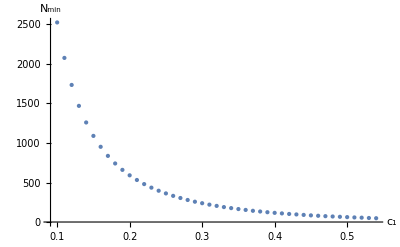

```mathematica
Yw3 = ListPlot[{{0.1,2526},
{0.11,2077},
{0.12,1735},
{0.13,1470},
{0.14,1260},
{0.15,1090},
{0.16,952},
{0.17,837},
{0.18,741},
{0.19,660},
{0.20,591},
{0.21,532},
{0.22,480},
{0.23,435},
{0.24,396},
{0.25,362},
{0.26,331},
{0.27,304},
{0.28,279},{0.29,257},
{0.30,238},
{0.31,220},
{0.32,204},
{0.33,189},
{0.34,176},
{0.35,164},
{0.36,153},
{0.37,142},
{0.38,133},
{0.39,124},
{0.40,116},
{0.41,109},
{0.42,102},
{0.43,96},
{0.44,90},
{0.45,84},
{0.46,79},
{0.47,74},
{0.48,70},
{0.49,66},
{0.50,62},
{0.51,58},
{0.52,55},
{0.53,51},
{0.54,48}(*,
{0.55,46},
{0.56,43},
{0.57,40}*)},AxesLabel->{Style[Subscript[c,1],Black,Bold,15],Style[Subscript[N,min],Black,Bold,15]},AxesStyle->{{Bold,Black},{Bold,Black}},
TicksStyle->Directive[FontSize->13],PlotStyle->{PointSize->Large}]
```

```mathematica
Show[Yw3,Xw3,Zw3]
```

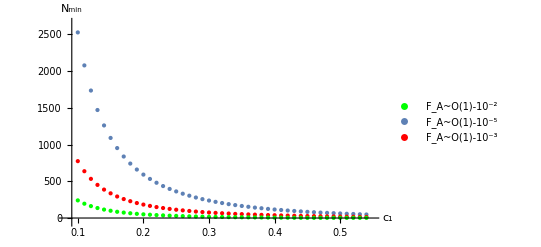

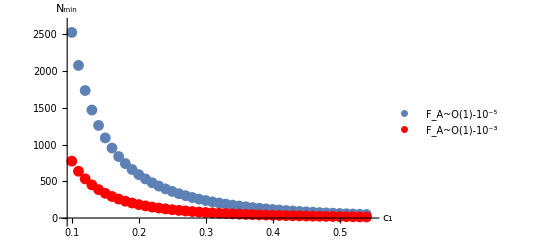

```mathematica
c2=√(1-c0^2-c1^2);c0=0.45;
For[c1=0.1,c1<1/√3,c1+=0.01,
	For[cp=2,cp<20000,cp++,
If[(√(3+((1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (-3+(c0+c1+c2)^2))/(-3 c0^2 c1^2+c2^2)))/(√3)>0.9999,Break[]]]Print[{c1,cp}]]
Clear[c0,c1,c2,cp]
```

{0.1,951}

{0.11,780}

{0.12,651}

{0.13,550}

{0.14,471}

{0.15,406}

{0.16,354}

{0.17,311}

{0.18,274}

{0.19,244}

{0.2,218}

{0.21,195}

{0.22,176}

{0.23,159}

{0.24,144}

{0.25,131}

{0.26,119}

{0.27,109}

{0.28,100}

{0.29,92}

{0.3,84}

{0.31,78}

{0.32,72}

{0.33,66}

{0.34,61}

{0.35,57}

{0.36,52}

{0.37,48}

{0.38,45}

{0.39,42}

{0.4,39}

{0.41,36}

{0.42,33}

{0.43,31}

{0.44,29}

{0.45,27}

{0.46,25}

{0.47,23}

{0.48,21}

{0.49,20}

{0.5,18}

{0.51,17}

{0.52,16}

{0.53,15}

{0.54,13}

{0.55,12}

{0.56,12}

{0.57,11}

```mathematica
c2=√(1-c0^2-c1^2);c0=0.45;
For[c1=0.1,c1<1/√3,c1+=0.01,
	For[cp=2,cp<20000,cp++,
If[(√(3+((1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (-3+(c0+c1+c2)^2))/(-3 c0^2 c1^2+c2^2)))/(√3)>0.99,Break[]]]Print[{c1,cp}]]
Clear[c0,c1,c2,cp]
```

{0.1,357}
{0.11,291}
{0.12,241}
{0.13,203}
{0.14,172}
{0.15,148}
{0.16,128}
{0.17,112}
{0.18,98}
{0.19,86}
{0.2,76}
{0.21,68}
{0.22,61}
{0.23,55}
{0.24,49}
{0.25,44}
{0.26,40}
{0.27,36}
{0.28,33}
{0.29,30}
{0.3,27}
{0.31,25}
{0.32,23}
{0.33,21}
{0.34,19}
{0.35,17}
{0.36,16}
{0.37,14}
{0.38,13}
{0.39,12}
{0.4,11}
{0.41,10}
{0.42,9}
{0.43,8}
{0.44,8}
{0.45,7}
{0.46,6}
{0.47,6}
{0.48,5}
{0.49,5}
{0.5,4}
{0.51,4}
{0.52,3}
{0.53,3}
{0.54,3}
{0.55,3}
{0.56,2}
{0.57,2}

```mathematica
c2=√(1-c0^2-c1^2);c0=0.45;
For[c1=0.1,c1<1/√3,c1+=0.01,
	For[cp=2,cp<20000,cp++,
If[(√(3+((1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (-3+(c0+c1+c2)^2))/(-3 c0^2 c1^2+c2^2)))/(√3)>0.9,Break[]]]Print[{c1,cp}]]
Clear[c0,c1,c2,cp]
```

{0.1,65}
{0.11,51}
{0.12,40}
{0.13,32}
{0.14,26}
{0.15,21}
{0.16,17}
{0.17,14}
{0.18,11}
{0.19,9}
{0.2,7}
{0.21,6}
{0.22,4}
{0.23,3}
{0.24,2}
{0.25,2}
{0.26,2}
{0.27,2}
{0.28,2}
{0.29,2}
{0.3,2}
{0.31,2}
{0.32,2}
{0.33,2}
{0.34,2}
{0.35,2}
{0.36,2}
{0.37,2}
{0.38,2}
{0.39,2}
{0.4,2}
{0.41,2}
{0.42,2}
{0.43,2}
{0.44,2}
{0.45,2}
{0.46,2}
{0.47,2}
{0.48,2}
{0.49,2}
{0.5,2}
{0.51,2}
{0.52,2}
{0.53,2}
{0.54,2}
{0.55,2}
{0.56,2}
{0.57,2}

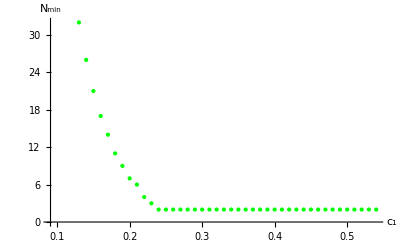

```mathematica
Zw45=ListPlot[{{0.1,65},
{0.11,51},
{0.12,40},
{0.13,32},
{0.14,26},
{0.15000000000000002,21},
{0.16000000000000003,17},
{0.17000000000000004,14},
{0.18000000000000005,11},
{0.19000000000000006,9},
{0.20000000000000007,7},
{0.21000000000000008,6},
{0.22000000000000008,4},
{0.2300000000000001,3},
{0.2400000000000001,2},
{0.2500000000000001,2},
{0.2600000000000001,2},
{0.27000000000000013,2},
{0.28000000000000014,2},
{0.29000000000000015,2},
{0.30000000000000016,2},
{0.31000000000000016,2},
{0.3200000000000002,2},
{0.3300000000000002,2},
{0.3400000000000002,2},
{0.3500000000000002,2},
{0.3600000000000002,2},
{0.3700000000000002,2},
{0.3800000000000002,2},
{0.39000000000000024,2},
{0.40000000000000024,2},
{0.41000000000000025,2},
{0.42000000000000026,2},
{0.43000000000000027,2},
{0.4400000000000003,2},
{0.4500000000000003,2},
{0.4600000000000003,2},
{0.4700000000000003,2},
{0.4800000000000003,2},
{0.4900000000000003,2},
{0.5000000000000003,2},
{0.5100000000000003,2},
{0.5200000000000004,2},
{0.5300000000000004,2},
{0.5400000000000004,2}(*
{0.5500000000000004,2}
{0.5600000000000004,2}
{0.5700000000000004,2}*)},AxesLabel->{Style[Subscript[c,1],Black,Bold,15],Style[Subscript[N,min],Black,Bold,15]},AxesStyle->{{Bold,Black},{Bold,Black}},
TicksStyle->Directive[FontSize->13],PlotStyle->{PointSize->Large,Green}]
```

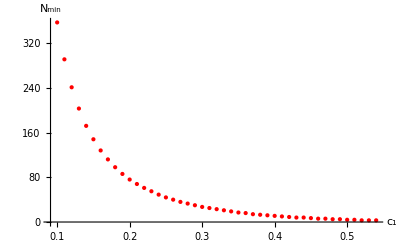

```mathematica
Xw45=ListPlot[{{0.1,357},
{0.11,291},
{0.12,241},
{0.13,203},
{0.14,172},
{0.15000000000000002,148},
{0.16000000000000003,128},
{0.17000000000000004,112},
{0.18000000000000005,98},
{0.19000000000000006,86},
{0.20000000000000007,76},
{0.21000000000000008,68},
{0.22000000000000008,61},
{0.2300000000000001,55},
{0.2400000000000001,49},
{0.2500000000000001,44},
{0.2600000000000001,40},
{0.27000000000000013,36},
{0.28000000000000014,33},
{0.29000000000000015,30},
{0.30000000000000016,27},
{0.31000000000000016,25},
{0.3200000000000002,23},
{0.3300000000000002,21},
{0.3400000000000002,19},
{0.3500000000000002,17},
{0.3600000000000002,16},
{0.3700000000000002,14},
{0.3800000000000002,13},
{0.39000000000000024,12},
{0.40000000000000024,11},
{0.41000000000000025,10},
{0.42000000000000026,9},
{0.43000000000000027,8},
{0.4400000000000003,8},
{0.4500000000000003,7},
{0.4600000000000003,6},
{0.4700000000000003,6},
{0.4800000000000003,5},
{0.4900000000000003,5},
{0.5000000000000003,4},
{0.5100000000000003,4},
{0.5200000000000004,3},
{0.5300000000000004,3},
{0.5400000000000004,3}(*,
{0.5500000000000004,3},
{0.5600000000000004,2},
{0.5700000000000004,2}*)},AxesLabel->{Style[Subscript[c,1],Black,Bold,15],Style[Subscript[N,min],Black,Bold,15]},AxesStyle->{{Bold,Black},{Bold,Black}},
TicksStyle->Directive[FontSize->13],PlotStyle->{PointSize->Large,Red}]
```

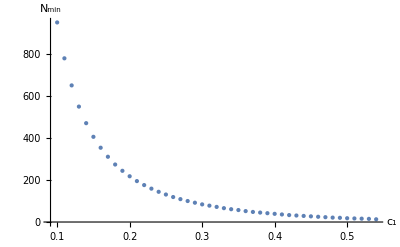

```mathematica
Yw45=ListPlot[{{0.1,951},{0.11,780},
{0.12,651},
{0.13,550},
{0.14,471},
{0.15,406},
{0.16,354},
{0.17,311},
{0.18,274},
{0.19,244},
{0.20,218},
{0.21,195},
{0.22,176},
{0.23,159},
{0.24,144},
{0.25,131},
{0.26,119},
{0.27,109},
{0.28,100},
{0.29,92},
{0.30,84},
{0.31,78},
{0.32,72},
{0.33,66},
{0.34,61},
{0.35,57},
{0.36,52},
{0.37,48},
{0.38,45},
{0.39,42},
{0.40,39},
{0.41,36},
{0.42,33},
{0.43,31},
{0.44,29},
{0.45,27},
{0.46,25},
{0.47,23},
{0.48,21},
{0.49,20},
{0.50,18},
{0.51,17},
{0.52,16},
{0.53,15},
{0.54,13}(*,
{0.55,12},
{0.56,12},
{0.57,11}*)},AxesLabel->{Style[Subscript[c,1],Black,Bold,15],Style[Subscript[N,min],Black,Bold,15]},AxesStyle->{{Bold,Black},{Bold,Black}},
TicksStyle->Directive[FontSize->13],PlotStyle->{PointSize->Large}]
```

```mathematica
Show[Yw45,Xw45,Zw45]
```

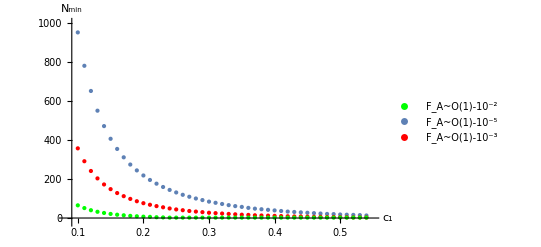

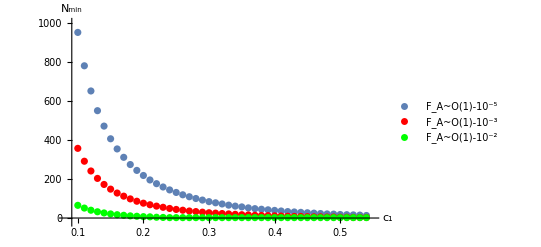

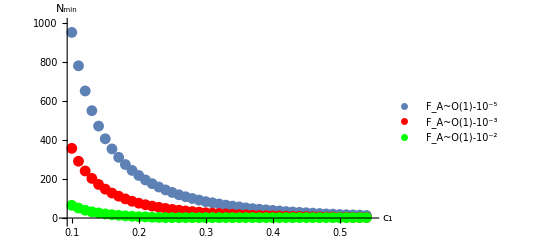

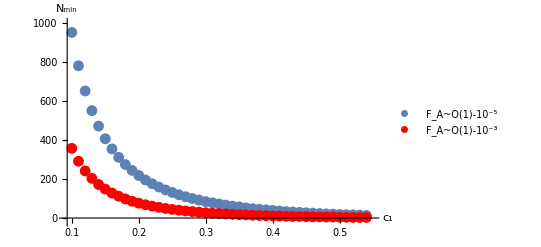

```mathematica
1/3 (√(1+(-1+3 c2^2) (X)^(N-1))+√((4 c2^2+12 c1^2 (-1+c1^2+c2^2)+6 c1 c2^2 √(1-c1^2-c2^2) (X)^N-(c2^2+3 c2^4) (X)^N)/(c2^2+3 c1^2 (-1+c1^2+c2^2))))
```

```mathematica
FullSimplify[Fw[1]]
```

(√(3+((1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (-3+(c0+c1+c2)^2))/(-3 c0^2 c1^2+c2^2)))/(√3)

```mathematica
FullSimplify[Fw[2]]
```

(√(3+((1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (-3+(c0+c1+c2)^2))/(-3 c0^2 c1^2+c2^2)))/(√3)

```mathematica
FullSimplify[Fw[3]]
```

1/3 (√(1-(1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+3 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp) c2^2)+√(4-((-4+3 (c0+c1)^2) (1-(3 c0^2 c1^2)/c2^2)^cp c2^2)/(3 c0^2 c1^2-c2^2)))

```mathematica
c1=1/√3;c2=√2/√3-0.01;(*c0=√(1-c1^2-c2^2);*)(*cp=2;*)
(*FullSimplify[9 Fw[3]^2-9 Fw[1]^2]*)
FullSimplify[9 Fw[3]^2-9 Fw[1]^2]
FullSimplify[9 Fw[1]^2]
Simplify[c0]
Clear[c0,c1,c2,cp]
```

-4+1.20621 (1-1.53743 c0^2)^(-1+cp)-4.83898 c0 (1-1.53743 c0^2)^(-1+cp)+6 √(1+0.95131 (1-1.53743 c0^2)^(-1+cp)) √((-0.289083+0.444444 c0^2+(0.216812+(-0.250353-0.216812 c0) c0) (1-1.53743 c0^2)^cp)/(-0.650437+1. c0^2))

(-5.85393+9. c0^2+(2.11711+(-5.40063-1.95131 c0) c0) (1-1.53743 c0^2)^cp)/(-0.650437+1. c0^2)

c0

```mathematica
c0=√(2/3-0.65);
Simplify[-4+1.206213891405187 (1-1.537428540111639 c0^2)^(-1+cp)-4.838979485566356 c0 (1-1.537428540111639 c0^2)^(-1+cp)+6 √(1+0.9513102051443365 (1-1.537428540111639 c0^2)^(-1+cp)) √((-0.2890829933547165+0.4444444444444444 c0^2+(0.21681224501603732+(-0.2503532160472326-0.21681224501603738 c0) c0) (1-1.537428540111639 c0^2)^cp)/(-0.6504367350481122+1. c0^2))]
Clear[c0]
```

-4.+0.596797 0.974376^cp+7.53677 √(0.281676-0.180878 0.974376^cp) √(1+0.976327 0.974376^cp)

```mathematica
(√(3+(X^N c2^2 (-3+(c0+c1+c2)^2))/(-3 c0^2 c1^2+c2^2)))/(√3)
```

```mathematica
1/3 (√(1-(X)^(N-1)+3 (X)^(N-1) c2^2)+√(4-((-4+3 (c0+c1)^2) (X)^N c2^2)/(3 c0^2 c1^2-c2^2)))
```

```mathematica
c2=√(1-c0^2-c1^2);cp=21;
Plot3D[{Fw[1],Fw[2],Fw[3]},{c0,0.01,1/√3},{c1,0.01,1/√3},PlotStyle->{Red,Black,Blue}]
Clear[c2,cp]
```

-Graphics3D-

```mathematica
Assemblages in 2SDI (*(Distillation not possible)*)
```

2 Assemblages Distillation in not possible SDI

```mathematica
For[l=1,l<4,l++,
For[k=1,k<4,k++,
For[i=0,i<2,i++,
For[j=0,j<2,j++,
c2=c1;c1=√((1-c0^2)/2);
Sw[i,j,l,k]=Simplify[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,(σ[0]+(-1)^j σ[k])/2,σ[0]].ρw.ConjugateTranspose[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,(σ[0]+(-1)^j σ[k])/2,σ[0]]]];
(*Print[MatrixForm[Sw[i,j,k,l]]];*)
sw[i,j,l,k]=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].Sw[i,j,l,k].KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].Sw[i,j,l,k].KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].Sw[i,j,l,k].KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].Sw[i,j,l,k].KroneckerProduct[d,d,σ[0]]];
Print[{i,j,l-1,k-1}];
Print[MatrixForm[sw[i,j,l,k]]];
C0=({{c0/c1, 0}, {0, 1}});
(*c2=c1;*)
(*Print[MatrixForm[Simplify[C0.sw[i,j,l,k].C0]]];*)
Clear[C0];
c0=1/(√3);c1=1/(√3);c2=1/(√3);
gw[i,j,l,k]=sw[i,j,l,k];
(*Print[MatrixForm[gw[i,j,l,k]]];*)
Clear[c0,c1,c2];
Pgwf=Simplify[(1-(3 c0^2))^(cp-1)];Pgs=Simplify[1-(1-(3 c0^2))^(cp-1)];
gDw[i,j,l,k]=Simplify[Pgs*gw[i,j,l,k]+Pgwf*sw[i,j,l,k]];(*Print[MatrixForm[gDw[i,j,l,k]]]*)]]]]
Clear[l,i,j,k,c2,c1,c0,C0]
```

{0,0,0,0}

(1/2 (1-c0^2) | (c0 √(1-c0^2))/(2 √2)
(c0 √(1-c0^2))/(2 √2) | c0^2/4)

{0,1,0,0}

(0 | 0
0 | c0^2/4)

{1,0,0,0}

(0 | 0
0 | c0^2/4)

{1,1,0,0}

(1/2 (1-c0^2) | -(c0 √(1-c0^2))/(2 √2)
-(c0 √(1-c0^2))/(2 √2) | c0^2/4)

{0,0,0,1}

(1/4 (1-c0^2) | ((1/4-ⅈ/4) c0 √(1-c0^2))/(√2)
((1/4+ⅈ/4) c0 √(1-c0^2))/(√2) | c0^2/4)

{0,1,0,1}

(1/4 (1-c0^2) | ((1/4+ⅈ/4) c0 √(1-c0^2))/(√2)
((1/4-ⅈ/4) c0 √(1-c0^2))/(√2) | c0^2/4)

{1,0,0,1}

(1/4 (1-c0^2) | -((1/4+ⅈ/4) c0 √(1-c0^2))/(√2)
-((1/4-ⅈ/4) c0 √(1-c0^2))/(√2) | c0^2/4)

{1,1,0,1}

(1/4 (1-c0^2) | -((1/4-ⅈ/4) c0 √(1-c0^2))/(√2)
-((1/4+ⅈ/4) c0 √(1-c0^2))/(√2) | c0^2/4)

{0,0,0,2}

(1/4 (1-c0^2) | (c0 √(1-c0^2))/(2 √2)
(c0 √(1-c0^2))/(2 √2) | c0^2/2)

{0,1,0,2}

(1/4 (1-c0^2) | 0
0 | 0)

{1,0,0,2}

(1/4 (1-c0^2) | -(c0 √(1-c0^2))/(2 √2)
-(c0 √(1-c0^2))/(2 √2) | c0^2/2)

{1,1,0,2}

(1/4 (1-c0^2) | 0
0 | 0)

{0,0,1,0}

(1/4 (1-c0^2) | ((1/4-ⅈ/4) c0 √(1-c0^2))/(√2)
((1/4+ⅈ/4) c0 √(1-c0^2))/(√2) | c0^2/4)

{0,1,1,0}

(1/4 (1-c0^2) | -((1/4+ⅈ/4) c0 √(1-c0^2))/(√2)
-((1/4-ⅈ/4) c0 √(1-c0^2))/(√2) | c0^2/4)

{1,0,1,0}

(1/4 (1-c0^2) | ((1/4+ⅈ/4) c0 √(1-c0^2))/(√2)
((1/4-ⅈ/4) c0 √(1-c0^2))/(√2) | c0^2/4)

{1,1,1,0}

(1/4 (1-c0^2) | -((1/4-ⅈ/4) c0 √(1-c0^2))/(√2)
-((1/4+ⅈ/4) c0 √(1-c0^2))/(√2) | c0^2/4)

{0,0,1,1}

(1/2 (1-c0^2) | -(ⅈ c0 √(1-c0^2))/(2 √2)
(ⅈ c0 √(1-c0^2))/(2 √2) | c0^2/4)

{0,1,1,1}

(0 | 0
0 | c0^2/4)

{1,0,1,1}

(0 | 0
0 | c0^2/4)

{1,1,1,1}

(1/2 (1-c0^2) | (ⅈ c0 √(1-c0^2))/(2 √2)
-(ⅈ c0 √(1-c0^2))/(2 √2) | c0^2/4)

{0,0,1,2}

(1/4 (1-c0^2) | -(ⅈ c0 √(1-c0^2))/(2 √2)
(ⅈ c0 √(1-c0^2))/(2 √2) | c0^2/2)

{0,1,1,2}

(1/4 (1-c0^2) | 0
0 | 0)

{1,0,1,2}

(1/4 (1-c0^2) | (ⅈ c0 √(1-c0^2))/(2 √2)
-(ⅈ c0 √(1-c0^2))/(2 √2) | c0^2/2)

{1,1,1,2}

(1/4 (1-c0^2) | 0
0 | 0)

{0,0,2,0}

(1/4 (1-c0^2) | (c0 √(1-c0^2))/(2 √2)
(c0 √(1-c0^2))/(2 √2) | c0^2/2)

{0,1,2,0}

(1/4 (1-c0^2) | -(c0 √(1-c0^2))/(2 √2)
-(c0 √(1-c0^2))/(2 √2) | c0^2/2)

{1,0,2,0}

(1/4 (1-c0^2) | 0
0 | 0)

{1,1,2,0}

(1/4 (1-c0^2) | 0
0 | 0)

{0,0,2,1}

(1/4 (1-c0^2) | -(ⅈ c0 √(1-c0^2))/(2 √2)
(ⅈ c0 √(1-c0^2))/(2 √2) | c0^2/2)

{0,1,2,1}

(1/4 (1-c0^2) | (ⅈ c0 √(1-c0^2))/(2 √2)
-(ⅈ c0 √(1-c0^2))/(2 √2) | c0^2/2)

{1,0,2,1}

(1/4 (1-c0^2) | 0
0 | 0)

{1,1,2,1}

(1/4 (1-c0^2) | 0
0 | 0)

{0,0,2,2}

(0 | 0
0 | c0^2)

{0,1,2,2}

(1/2 (1-c0^2) | 0
0 | 0)

{1,0,2,2}

(1/2 (1-c0^2) | 0
0 | 0)

{1,1,2,2}

(0 | 0
0 | 0)

```mathematica
(*c0=1/(√3);*)
MatrixForm[sw[0,0,2,3]]
Simplify[Tr[Sw[0,0,2,3]]]
Clear[c0]
```

(1/4 (1-c0^2) | -(ⅈ c0 √(1-c0^2))/(2 √2)
(ⅈ c0 √(1-c0^2))/(2 √2) | c0^2/2)

1/4 (1+c0^2)

```mathematica
(*c0=1/√3;*)
g=Simplify[(*1/(√2)*)√((1-d0^2)/2)(1)u+ (I d0)/2 d];
gT=Simplify[ConjugateTranspose[g],0<d0<1];
MatrixForm[g.gT]
Simplify[Tr[g.gT]]
Clear[d0]
```

(1/2 (1-d0^2) | -(ⅈ d0 √(1-d0^2))/(2 √2)
(ⅈ d0 √(1-d0^2))/(2 √2) | d0^2/4)

1/4 (2-d0^2)

```mathematica
Simplify[Tr[({{1/2 (1-c0^2), (c0 √(1-c0^2))/(2 √2)}, {(c0 √(1-c0^2))/(2 √2), c0^2/4}}).({{1/2 (1-c0^2), (-c0 √(1-c0^2))/(2 √2)}, {(-c0 √(1-c0^2))/(2 √2), c0^2/4}})]]
```

1/16 (2-3 c0^2)^2

```mathematica
Probability of getting outcome 0 in 2SDI w-state
```

```mathematica
c1=√((1-c0^2)/2);
C0=({{c0/c1, 0}, {0, 1}});
P12SW=Simplify[Tr[C0.(sw[0,0,1,1]+sw[0,1,1,1]+sw[1,0,1,1]+sw[1,1,1,1]).C0]];
P22sW=Simplify[Tr[C0.(sw[0,0,2,1]+sw[0,1,2,1]+sw[1,0,2,1]+sw[1,1,2,1]).C0]];
P32SW=Simplify[Tr[C0.(sw[0,0,3,1]+sw[0,1,3,1]+sw[1,0,3,1]+sw[1,1,3,1]).C0]];
P42sW=Simplify[Tr[C0.(sw[0,0,1,2]+sw[0,1,1,2]+sw[1,0,1,2]+sw[1,1,1,2]).C0]];
P52SW=Simplify[Tr[C0.(sw[0,0,1,3]+sw[0,1,1,3]+sw[1,0,1,3]+sw[1,1,1,3]).C0]];
P62SW=Simplify[Tr[C0.(sw[0,0,2,2]+sw[0,1,2,2]+sw[1,0,2,2]+sw[1,1,2,2]).C0]];
P72SW=Simplify[Tr[C0.(sw[0,0,3,2]+sw[0,1,3,2]+sw[1,0,3,2]+sw[1,1,3,2]).C0]];
P82SW=Simplify[Tr[C0.(sw[0,0,2,3]+sw[0,1,2,3]+sw[1,0,2,3]+sw[1,1,2,3]).C0]];
P92SW=Simplify[Tr[C0.(sw[0,0,3,3]+sw[0,1,3,3]+sw[1,0,3,3]+sw[1,1,3,3]).C0]];
For[l=1,l<4,l++,
For[k=1,k<4,k++,
For[i=0,i<2,i++,
For[j=0,j<2,j++,
P2SW[l,k]=Simplify[Sum[Tr[C0.sw[i,j,l,k].C0],{i,0,1,1},{j,0,1,1}]]]]Print[{l-1,k-1}];Print[P2SW[l,k]]]]
Clear[C0,c1]
```

{0,0}

3 c0^2

{0,1}

3 c0^2

{0,2}

3 c0^2

{1,0}

3 c0^2

{1,1}

3 c0^2

{1,2}

3 c0^2

{2,0}

3 c0^2

{2,1}

3 c0^2

{2,2}

3 c0^2

```mathematica
Assemblage fidelity of w-state in 2SDI
```

```mathematica
Fw2S0000=FullSimplify[√Tr[gw[0,0,1,1].gDw[0,0,1,1]](*+√Tr[gw[0,1,1,1].gDw[0,1,1,1]]+√Tr[gw[1,0,1,1].gDw[1,0,1,1]]+√Tr[gw[1,1,1,1].gDw[1,1,1,1]]*)]
```

1/12 √((-25+(1-3 c0^2)^cp+3 c0 (-4 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (25+7 (1-3 c0^2)^cp)))/(-1+3 c0^2))

```mathematica
Fw2S22=Simplify[√Tr[gw[0,0,2,2].gDw[0,0,2,2]]+√Tr[gw[0,1,2,2].gDw[0,1,2,2]]+√Tr[gw[1,0,2,2].gDw[1,0,2,2]]+√Tr[gw[1,1,2,2].gDw[1,1,2,2]]]
```

1/6 (√(1-(1-3 c0^2)^cp)+√((-25+(1-3 c0^2)^cp-12 c0 (1-3 c0^2)^cp √(2-2 c0^2)+3 c0^2 (25+7 (1-3 c0^2)^cp))/(-1+3 c0^2)))

```mathematica
Fw2S01=Simplify[√Tr[gw[0,0,1,2].gDw[0,0,1,2]]+√Tr[gw[0,1,1,2].gDw[0,1,1,2]]+√Tr[gw[1,0,1,2].gDw[1,0,1,2]]+√Tr[gw[1,1,1,2].gDw[1,1,1,2]]]
```

√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2))

```mathematica
Fw2S10=Simplify[√Tr[gw[0,0,2,1].gDw[0,0,2,1]]+√Tr[gw[0,1,2,1].gDw[0,1,2,1]]+√Tr[gw[1,0,2,1].gDw[1,0,2,1]]+√Tr[gw[1,1,2,1].gDw[1,1,2,1]]]
```

√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2))

```mathematica
Fw2S02=Simplify[√Tr[gw[0,0,1,3].gDw[0,0,1,3]]+√Tr[gw[0,1,1,3].gDw[0,1,1,3]]+√Tr[gw[1,0,1,3].gDw[1,0,1,3]]+√Tr[gw[1,1,1,3].gDw[1,1,1,3]]]
```

(√(2+(1-3 c0^2)^cp)+√((-8+5 (1-3 c0^2)^cp-6 c0 (1-3 c0^2)^cp √(2-2 c0^2)-3 c0^2 (-8+(1-3 c0^2)^cp))/(-1+3 c0^2)))/(3 √2)

```mathematica
Expand[(√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2)))-(1/(√3)(√(3-2(c0-√((1-c0^2)/2))^2(1-3 d0^2)^(cp-1))))]
```

√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2))-(√(3-2 (c0-(√(1-c0^2))/(√2))^2 (1-3 d0^2)^(-1+cp)))/(√3)

```mathematica
FullSimplify[(1/6 (√(1-(1-3 c0^2)^cp)+√((-25+(1-3 c0^2)^cp+3 c0 (-4 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (25+7 (1-3 c0^2)^cp)))/(-1+3 c0^2))))-(1/6 (√(1-(1-3 c0^2)^cp)+√(25-(1-3 c0^2)^(cp-1)(1+21 c0^2-12c0 √(2-2 c0^2) ))))]
```

0

```mathematica
FullSimplify[(√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2)))-(1/(√3)√(3-2(√((1-c0^2)/2)-c0)^2(1-3 c0^2)^(cp-1)))]
```

0

```mathematica
FullSimplify[((√(2+(1-3 c0^2)^cp)+√((-8+5 (1-3 c0^2)^cp-3 c0 (2 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (-8+(1-3 c0^2)^cp)))/(-1+3 c0^2)))/(3 √2))-(1/(3 √2)(√(2+(1-3 c0^2)^cp)+√(8+ (1-3 c0^2)^(cp-1)(6 c0 √(2-2 c0^2)+3 c0^2-5))))]
```

0

```mathematica
For[l=1,l<4,l++,
For[k=1,k<4,k++,
F2Sw[l,k]=FullSimplify[Sum[√Tr[gw[i,j,l,k].gDw[i,j,l,k]],{i,0,1,1},{j,0,1,1}]];Print[{l-1,k-1}];Print[F2Sw[l,k]]]]
```

{0,0}

1/6 (√(1-(1-3 c0^2)^cp)+√((-25+(1-3 c0^2)^cp+3 c0 (-4 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (25+7 (1-3 c0^2)^cp)))/(-1+3 c0^2)))

{0,1}

√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2))

{0,2}

(√(2+(1-3 c0^2)^cp)+√((-8+5 (1-3 c0^2)^cp-3 c0 (2 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (-8+(1-3 c0^2)^cp)))/(-1+3 c0^2)))/(3 √2)

{1,0}

√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2))

{1,1}

1/6 (√(1-(1-3 c0^2)^cp)+√((-25+(1-3 c0^2)^cp+3 c0 (-4 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (25+7 (1-3 c0^2)^cp)))/(-1+3 c0^2)))

{1,2}

(√(2+(1-3 c0^2)^cp)+√((-8+5 (1-3 c0^2)^cp-3 c0 (2 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (-8+(1-3 c0^2)^cp)))/(-1+3 c0^2)))/(3 √2)

{2,0}

(√(2+(1-3 c0^2)^cp)+√((-8+5 (1-3 c0^2)^cp-3 c0 (2 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (-8+(1-3 c0^2)^cp)))/(-1+3 c0^2)))/(3 √2)

{2,1}

(√(2+(1-3 c0^2)^cp)+√((-8+5 (1-3 c0^2)^cp-3 c0 (2 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (-8+(1-3 c0^2)^cp)))/(-1+3 c0^2)))/(3 √2)

{2,2}

1/3 (√(1-(1-3 c0^2)^cp)+√2 √(2+(1-3 c0^2)^cp))

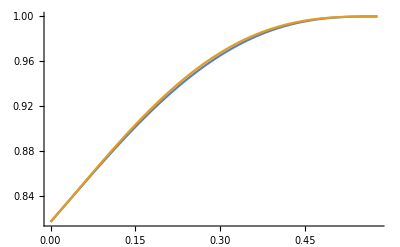

```mathematica
cp=2;
Plot[{(*F2Sw[1,1],*)F2Sw[1,2],F2Sw[1,3](*,F2Sw[3,3]*)},{c0,0,1/√3}]
Clear[cp]
```

```mathematica
F2Sw[0,1] is minimum and it is shown as F0
```

```mathematica
FullSimplify[(1/18(10+(1-3 c0^2)^cp+(3 c0^2+6c0 √(2-2 c0^2)-5)(1-3 c0^2)^(cp-1)))-(1/9+1/18 (1-3 c0^2)^cp-4/(9 (-1+3 c0^2))+(4 c0^2)/(3 (-1+3 c0^2))+(5 (1-3 c0^2)^cp)/(18 (-1+3 c0^2))-(c0^2 (1-3 c0^2)^cp)/(6 (-1+3 c0^2))-(c0 (1-3 c0^2)^cp √(2-2 c0^2))/(3 (-1+3 c0^2)))]
```

0

```mathematica
Simplify[Expand[(√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2)))^2-(1/9+1/18 (1-3 c0^2)^cp-4/(9 (-1+3 c0^2))+(4 c0^2)/(3 (-1+3 c0^2))+(5 (1-3 c0^2)^cp)/(18 (-1+3 c0^2))-(c0^2 (1-3 c0^2)^cp)/(6 (-1+3 c0^2))-(c0 (1-3 c0^2)^cp √(2-2 c0^2))/(3 (-1+3 c0^2)))]]
```

(-4+(1-3 c0^2)^cp-3 c0 (1-3 c0^2)^cp √(2-2 c0^2)+3 c0^2 (4+(1-3 c0^2)^cp))/(-9+27 c0^2)

```mathematica
FullSimplify[((-4+(1-3 c0^2)^cp-3 c0 (1-3 c0^2)^cp √(2-2 c0^2)+3 c0^2 (4+(1-3 c0^2)^cp))/(-9+27 c0^2))-(1/9(4(1-(1-3 c0^2)^(cp-1))+3(c0 √(2-2 c0^2)+(1-c0^2))(1-3 c0^2)^(cp-1)))]
```

0

```mathematica
(4-Y^N+3 c0 Y^N √(2-2 c0^2)-3 c0^2 (4+Y^N))/(9Y)
```

```mathematica
Simplify[Expand[((-4+(1-3 c0^2)^cp-3 c0 (1-3 c0^2)^cp √(2-2 c0^2)+3 c0^2 (4+(1-3 c0^2)^cp))/(-9+27 c0^2))^2]]
```

1/(81 (1-3 c0^2)^2)(-6 c0 (1-3 c0^2)^cp √(2-2 c0^2) (-4+(1-3 c0^2)^cp)+(-4+(1-3 c0^2)^cp)^2-18 c0^3 (1-3 c0^2)^cp √(2-2 c0^2) (4+(1-3 c0^2)^cp)+24 c0^2 (-4+(1-3 c0^2)^(2 cp))-9 c0^4 (-16-8 (1-3 c0^2)^cp+(1-3 c0^2)^(2 cp)))

```mathematica
F(0,2) assemblage fidelity shown as F3
```

```mathematica
1/9+1/18 Y^N+4/(9 Y)-(4 c0^2)/(3 Y)-(5 Y^(N-1))/18+(c0^2 Y^(N-1))/6+(c0 Y^(N-1) √(2-2 c0^2))/3
```

```mathematica
Expand[((√(2+(1-3 c0^2)^cp)+√((-8+5 (1-3 c0^2)^cp-3 c0 (2 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (-8+(1-3 c0^2)^cp)))/(-1+3 c0^2)))/(3 √2))^2-(1/9+1/18 (1-3 c0^2)^cp-4/(9 (-1+3 c0^2))+(4 c0^2)/(3 (-1+3 c0^2))+(5 (1-3 c0^2)^cp)/(18 (-1+3 c0^2))-(c0^2 (1-3 c0^2)^cp)/(6 (-1+3 c0^2))-(c0 (1-3 c0^2)^cp √(2-2 c0^2))/(3 (-1+3 c0^2)))]
```

1/9 √(2+(1-3 c0^2)^cp) √((-8+5 (1-3 c0^2)^cp-3 c0 (2 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (-8+(1-3 c0^2)^cp)))/(-1+3 c0^2))

```mathematica
FullSimplify[(1/9 √(2+(1-3 c0^2)^cp) √((-8+5 (1-3 c0^2)^cp-3 c0 (2 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (-8+(1-3 c0^2)^cp)))/(-1+3 c0^2)))-(1/9 √(2+(1-3 c0^2)^cp) √(8+ (1-3 c0^2)^(cp-1)(6c0 √(2-2 c0^2)+3 c0^2-5)))]
```

0

```mathematica
1/9 √(2+Y^N) √((8-5 Y^N+3 c0 (2 Y^N √(2-2 c0^2)+c0 (-8+Y^N)))/Y)
```

```mathematica
Simplify[Expand[(1/9 √(2+(1-3 c0^2)^cp) √((-8+5 (1-3 c0^2)^cp-3 c0 (2 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (-8+(1-3 c0^2)^cp)))/(-1+3 c0^2)))^2]]
```

-((2+(1-3 c0^2)^cp) (8-5 (1-3 c0^2)^cp+6 c0 (1-3 c0^2)^cp √(2-2 c0^2)+3 c0^2 (-8+(1-3 c0^2)^cp)))/(81 (-1+3 c0^2))

```mathematica
Difference between (F0^2-A)^2-(F2^2-A)^2
```

```mathematica
FullSimplify[1/(81 (1-3 c0^2)^2)(-6 c0 (1-3 c0^2)^cp √(2-2 c0^2) (-4+(1-3 c0^2)^cp)+(-4+(1-3 c0^2)^cp)^2-18 c0^3 (1-3 c0^2)^cp √(2-2 c0^2) (4+(1-3 c0^2)^cp)+24 c0^2 (-4+(1-3 c0^2)^(2 cp))-9 c0^4 (-16-8 (1-3 c0^2)^cp+(1-3 c0^2)^(2 cp)))-(-((2+(1-3 c0^2)^cp) (8-5 (1-3 c0^2)^cp+6 c0 (1-3 c0^2)^cp √(2-2 c0^2)+3 c0^2 (-8+(1-3 c0^2)^cp)))/(81 (-1+3 c0^2)))]
```

-2/27 (1-3 c0^2)^(-2+cp) (-1+3 c0^2+(1-3 c0^2)^cp) (-1-c0^2+2 c0 √(2-2 c0^2))

```mathematica
FullSimplify[(-2/27 (1-3 c0^2)^(-2+cp) (-1+3 c0^2+(1-3 c0^2)^cp) (-1-c0^2+2 c0 √(2-2 c0^2)))-(-4/27 (1-3 c0^2)^(-1+cp) (1-(1-3 c0^2)^(cp-1)) ( √((1- c0^2)/2)-c0)^2)]
```

0

```mathematica
-2/27 Y^(N-1) (Y^(N-1)-1) (-1-c0^2+2 c0 √(2-2 c0^2))
```

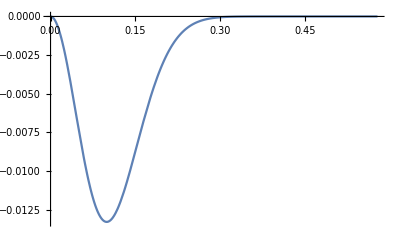

```mathematica
cp=20;
Plot[-2/27 (1-3 c0^2)^(-2+cp) (-1+3 c0^2+(1-3 c0^2)^cp) (-1-c0^2+2 c0 √(2-2 c0^2)),{c0,0,1/√3}]
Clear[cp]
```

```mathematica
F(0,0) is shown as F2
```

```mathematica
Expand[(1/6 (√(1-(1-3 c0^2)^cp)+√((-25+(1-3 c0^2)^cp+3 c0 (-4 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (25+7 (1-3 c0^2)^cp)))/(-1+3 c0^2))))^2]
```

1/36-1/36 (1-3 c0^2)^cp-25/(36 (-1+3 c0^2))+(25 c0^2)/(12 (-1+3 c0^2))+((1-3 c0^2)^cp)/(36 (-1+3 c0^2))+(7 c0^2 (1-3 c0^2)^cp)/(12 (-1+3 c0^2))-(c0 (1-3 c0^2)^cp √(2-2 c0^2))/(3 (-1+3 c0^2))+1/18 √(1-(1-3 c0^2)^cp) √((-25+(1-3 c0^2)^cp+3 c0 (-4 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (25+7 (1-3 c0^2)^cp)))/(-1+3 c0^2))

```mathematica
FullSimplify[(1/36-1/36 (1-3 c0^2)^cp-25/(36 (-1+3 c0^2))+(25 c0^2)/(12 (-1+3 c0^2))+((1-3 c0^2)^cp)/(36 (-1+3 c0^2))+(7 c0^2 (1-3 c0^2)^cp)/(12 (-1+3 c0^2))-(c0 (1-3 c0^2)^cp √(2-2 c0^2))/(3 (-1+3 c0^2)))-(1/36(26-(1-3 c0^2)^cp-(1+21 c0^2-12c0 √(2-2 c0^2))(1-3 c0^2)^(cp-1)))]
```

0

```mathematica
1/18 √(1-Y^N) √((25-Y^N-3 c0 (-4 Y^N √(2-2 c0^2)+c0 (25+7 Y^N)))/Y)
```

```mathematica
Simplify[Expand[(1/6 (√(1-(1-3 c0^2)^cp)+√((-25+(1-3 c0^2)^cp+3 c0 (-4 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (25+7 (1-3 c0^2)^cp)))/(-1+3 c0^2))))^2-(1/36-1/36 (1-3 c0^2)^cp-25/(36 (-1+3 c0^2))+(25 c0^2)/(12 (-1+3 c0^2))+((1-3 c0^2)^cp)/(36 (-1+3 c0^2))+(7 c0^2 (1-3 c0^2)^cp)/(12 (-1+3 c0^2))-(c0 (1-3 c0^2)^cp √(2-2 c0^2))/(3 (-1+3 c0^2)))]]
```

1/18 √(1-(1-3 c0^2)^cp) √((-25+(1-3 c0^2)^cp+3 c0 (-4 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (25+7 (1-3 c0^2)^cp)))/(-1+3 c0^2))

```mathematica
Simplify[Expand[(√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2)))^2-(1/36-1/36 (1-3 c0^2)^cp-25/(36 (-1+3 c0^2))+(25 c0^2)/(12 (-1+3 c0^2))+((1-3 c0^2)^cp)/(36 (-1+3 c0^2))+(7 c0^2 (1-3 c0^2)^cp)/(12 (-1+3 c0^2))-(c0 (1-3 c0^2)^cp √(2-2 c0^2))/(3 (-1+3 c0^2)))]]
```

(-6 c0 (1-3 c0^2)^cp √(2-2 c0^2)-3 c0^2 (-5+(1-3 c0^2)^cp)+5 (-1+(1-3 c0^2)^cp))/(-18+54 c0^2)

```mathematica
(6 c0 Y^N √(2-2 c0^2)-3 c0^2 (5-Y^N)+5 (1-Y^N))/(18Y)
```

```mathematica
Simplify[Expand[((-6 c0 (1-3 c0^2)^cp √(2-2 c0^2)-3 c0^2 (-5+(1-3 c0^2)^cp)+5 (-1+(1-3 c0^2)^cp))/(-18+54 c0^2))^2-(1/18 √(1-(1-3 c0^2)^cp) √((-25+(1-3 c0^2)^cp+3 c0 (-4 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (25+7 (1-3 c0^2)^cp)))/(-1+3 c0^2)))^2]]
```

-2/27 (1-3 c0^2)^(-2+cp) (-1+3 c0^2+(1-3 c0^2)^cp) (-1-c0^2+2 c0 √(2-2 c0^2))

```mathematica
-2/27 Y^(N-1) (Y^(N-1)-1) (-1-c0^2+2 c0 √(2-2 c0^2))
```

```mathematica
FullSimplify[(-2/27 (1-3 c0^2)^(-2+cp) (-1+3 c0^2+(1-3 c0^2)^cp) (-1-c0^2+2 c0 √(2-2 c0^2)))-(-4/27 (1-3 c0^2)^(-1+cp) (1-(1-3 c0^2)^(cp-1)) ( √((1- c0^2)/2)-c0)^2)]
```

0

```mathematica
F(2,2)
```

```mathematica
Expand[(1/3 (√(1-(1-3 c0^2)^cp)+√2 √(2+(1-3 c0^2)^cp)))^2]
```

5/9+1/9 (1-3 c0^2)^cp+2/9 √2 √(1-(1-3 c0^2)^cp) √(2+(1-3 c0^2)^cp)

```mathematica
Simplify[Expand[(1/3 (√(1-(1-3 c0^2)^cp)+√2 √(2+(1-3 c0^2)^cp)))^2-(5/9+1/9 (1-3 c0^2)^cp)]]
```

2/9 √2 √(-(-1+(1-3 c0^2)^cp) (2+(1-3 c0^2)^cp))

```mathematica
2/9 √2 √((1-Y^N) (2+Y^N))
```

```mathematica
(5/9+1/9 Y^N)
```

```mathematica
Simplify[Expand[(√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2)))^2-(5/9+1/9 (1-3 c0^2)^cp)]]
```

(-4+12 c0^2+4 (1-3 c0^2)^cp-6 c0 (1-3 c0^2)^cp √(2-2 c0^2))/(-9+27 c0^2)

```mathematica
FullSimplify[((-4+12 c0^2+4 (1-3 c0^2)^cp-6 c0 (1-3 c0^2)^cp √(2-2 c0^2))/(-9+27 c0^2))-(1/9(4(1-(1-3 c0^2)^(cp-1))+6 c0 (1-3 c0^2)^(cp-1) √(2-2 c0^2)))]
```

0

```mathematica
(4-12 c0^2-4 Y^N+6 c0 Y^N √(2-2 c0^2))/(9Y)
```

```mathematica
Simplify[Expand[((-4+12 c0^2+4 (1-3 c0^2)^cp-6 c0 (1-3 c0^2)^cp √(2-2 c0^2))/(-9+27 c0^2))^2-(2/9 √2 √(-(-1+(1-3 c0^2)^cp) (2+(1-3 c0^2)^cp)))^2]]
```

-8/27 (1-3 c0^2)^(-2+cp) (-1+3 c0^2+(1-3 c0^2)^cp) (-1-c0^2+2 c0 √(2-2 c0^2))

```mathematica
FullSimplify[(-8/27 (1-3 c0^2)^(-2+cp) (-1+3 c0^2+(1-3 c0^2)^cp) (-1-c0^2+2 c0 √(2-2 c0^2)))-(-16/27 (1-3 c0^2)^(-1+cp)(1-(1-3 c0^2)^(cp-1)) ( √((1- c0^2)/2)-c0)^2)]
```

0

```mathematica
-8/27 Y^(N-1) (Y^(N-1)-1) (-1-c0^2+2 c0 √(2-2 c0^2))
```

```mathematica
c0=0.12;cp=2;
Simplify[F2Sw[1,1]]
Simplify[F2Sw[1,2]]
Simplify[F2Sw[1,3]]
Simplify[F2Sw[2,1]]
Simplify[F2Sw[2,2]]
Simplify[F2Sw[2,3]]
Simplify[F2Sw[3,1]]
Simplify[F2Sw[3,2]]
Simplify[F2Sw[3,3]]
Clear[c0,cp]
```

0.893185

0.885405

0.88691

0.885405

0.893185

0.88691

0.88691

0.88691

0.901826

```mathematica
d0          N=2               N=5                    N=10
0.15       0.901419    0.920874         0.944898
0.2       0.926021    0.950211         0.974042
0.3       0.965262    0.986632         0.997243
0.4       0.989275    0.998499         0.999943
0.5       0.998947    0.999984         1
```

```mathematica
N_min Calculations
```

```mathematica
For[c0=0.12,c0<1/√3,c0+=0.01,
	For[cp=2,cp<20000,cp++,
If[√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2))>0.99,Break[]]]Print[{c0,cp}]]
```

{0.12,57}
{0.13,47}
{0.14,40}
{0.15,35}
{0.16,30}
{0.17,26}
{0.18,23}
{0.19,20}
{0.2,18}
{0.21,16}
{0.22,14}
{0.23,13}
{0.24,12}
{0.25,10}
{0.26,9}
{0.27,9}
{0.28,8}
{0.29,7}
{0.3,6}
{0.31,6}
{0.32,5}
{0.33,5}
{0.34,4}
{0.35,4}
{0.36,4}
{0.37,3}
{0.38,3}
{0.39,3}
{0.4,3}
{0.41,2}
{0.42,2}
{0.43,2}
{0.44,2}
{0.45,2}
{0.46,2}
{0.47,2}
{0.48,2}
{0.49,2}
{0.5,2}
{0.51,2}
{0.52,2}
{0.53,2}
{0.54,2}
{0.55,2}
{0.56,2}
{0.57,2}

```mathematica
For[c0=0.12,c0<1/√3,c0+=0.01,
	For[cp=2,cp<20000,cp++,
If[√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2))>0.9999,Break[]]]Print[{c0,cp}]]
```

```mathematica
For[c0=0.12,c0<1/√3,c0+=0.01,
	For[cp=2,cp<20000,cp++,
If[√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2))>0.9999,Break[]]]Print[{c0,cp}]]
```

{0.12,161}

{0.13,136}

{0.14,116}

{0.15,100}

{0.16,87}

{0.17,77}

{0.18,68}

{0.19,60}

{0.2,54}

{0.21,48}

{0.22,44}

{0.23,39}

{0.24,36}

{0.25,33}

{0.26,30}

{0.27,27}

{0.28,25}

{0.29,23}

{0.3,21}

{0.31,19}

{0.32,18}

{0.33,17}

{0.34,15}

{0.35,14}

{0.36,13}

{0.37,12}

{0.38,11}

{0.39,10}

{0.4,10}

{0.41,9}

{0.42,8}

{0.43,8}

{0.44,7}

{0.45,7}

{0.46,6}

{0.47,6}

{0.48,5}

{0.49,5}

{0.5,4}

{0.51,4}

{0.52,3}

{0.53,3}

{0.54,3}

{0.55,2}

{0.56,2}

{0.57,2}

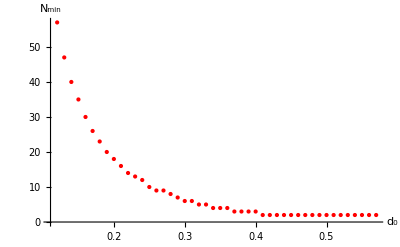

```mathematica
Xw2S=ListPlot[{{0.12,57},
{0.13,47},
{0.14,40},
{0.15000000000000002,35},
{0.16000000000000003,30},
{0.17000000000000004,26},
{0.18000000000000005,23},
{0.19000000000000006,20},
{0.20000000000000007,18},
{0.21000000000000008,16},
{0.22000000000000008,14},
{0.2300000000000001,13},
{0.2400000000000001,12},
{0.2500000000000001,10},
{0.2600000000000001,9},
{0.27000000000000013,9},
{0.28000000000000014,8},
{0.29000000000000015,7},
{0.30000000000000016,6},
{0.31000000000000016,6},
{0.3200000000000002,5},
{0.3300000000000002,5},
{0.3400000000000002,4},
{0.3500000000000002,4},
{0.3600000000000002,4},
{0.3700000000000002,3},
{0.3800000000000002,3},
{0.39000000000000024,3},
{0.40000000000000024,3},
{0.41000000000000025,2},
{0.42000000000000026,2},
{0.43000000000000027,2},
{0.4400000000000003,2},
{0.4500000000000003,2},
{0.4600000000000003,2},
{0.4700000000000003,2},
{0.4800000000000003,2},
{0.4900000000000003,2},
{0.5000000000000003,2},
{0.5100000000000003,2},
{0.5200000000000004,2},
{0.5300000000000004,2},
{0.5400000000000004,2},
{0.5500000000000004,2},
{0.5600000000000004,2},
{0.5700000000000004,2}},AxesLabel->{Style[Subscript[d,0],Black,Bold,15],Style[Subscript[N,min],Black,Bold,15]},AxesStyle->{{Bold,Black},{Bold,Black}},
TicksStyle->Directive[FontSize->13],PlotStyle->{PointSize->Large,Red}]
```

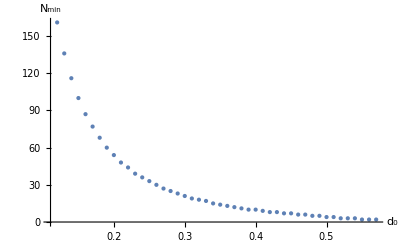

```mathematica
Yw2S=ListPlot[{
{0.12,161},
{0.13,136},
{0.14,116},
{0.15,100},
{0.16,87},
{0.17,77},
{0.18,68},
{0.19,60},
{0.20,54},
{0.21,48},
{0.22,44},
{0.23,39},
{0.24,36},
{0.25,33},
{0.26,30},
{0.27,27},
{0.28,25},
{0.29,23},
{0.30,21},
{0.31,19},
{0.32,18},
{0.33,17},
{0.34,15},
{0.35,14},
{0.36,13},
{0.37,12},
{0.38,11},
{0.39,10},
{0.40,10},
{0.41,9},
{0.42,8},
{0.43,8},
{0.44,7},
{0.45,7},
{0.46,6},
{0.47,6},
{0.48,5},
{0.49,5},
{0.50,4},
{0.51,4},
{0.52,3},
{0.53,3},
{0.54,3},
{0.55,2},
{0.56,2},
{0.57,2}},AxesLabel->{Style[Subscript[d,0],Black,Bold,15],Style[Subscript[N,min],Black,Bold,15]},AxesStyle->{{Bold,Black},{Bold,Black}},
TicksStyle->Directive[FontSize->13],PlotStyle->{PointSize->Large}]
```

```mathematica
Show[Yw2S,Xw2S]
```

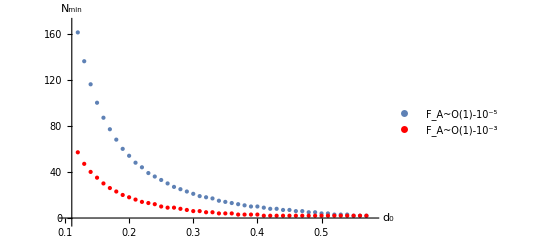

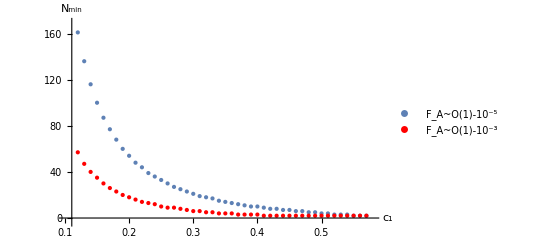

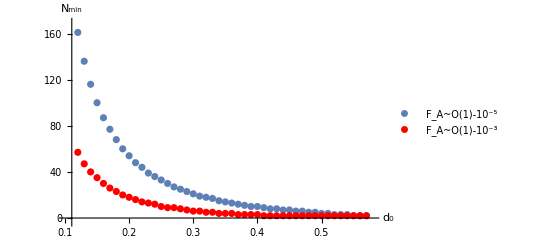

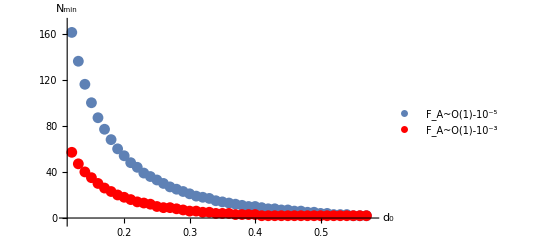

```mathematica
(*c0= (√2)/(√3(√(1+γ-λ)));c1=(√2)/(√3(√(1+γ+λ)));c2=(√2)/(√3(√(1+γ+λ)));*)
MatrixForm[Simplify[sw[0,0,2,1]-sw[1,1,1,2]]]
Simplify[Tr[Sw[0,0,1,2]]]
(*MatrixForm[gw[0,0,1,1]]
Simplify[Tr[gw[0,0,1,1]]]*)
Clear[c0,c1,c2]
```

(0 | ((1/2-ⅈ/2) c0 √(1-c0^2))/(√2)
((1/2+ⅈ/2) c0 √(1-c0^2))/(√2) | 0)

1/4

```mathematica
b=Simplify[√((1-c0^2)/2)((*I-*)1)u+ I c0 d];
bT=Simplify[ConjugateTranspose[b],{0<c0<1,0<c2<1,0<c1<1}];
MatrixForm[Simplify[1/2b.bT]]
```

(1/4 (1-c0^2) | -(ⅈ c0 √(1-c0^2))/(2 √2)
(ⅈ c0 √(1-c0^2))/(2 √2) | c0^2/2)

```mathematica
c=Simplify[(c1+ c2)u+I c0 d];
cT=Simplify[ConjugateTranspose[c],{0<c0<1,0<c2<1,0<c1<1}];
MatrixForm[Simplify[c.cT]]
```

((c1+c2)^2 | -ⅈ c0 (c1+c2)
ⅈ c0 (c1+c2) | c0^2)

```mathematica
θ=0;(*c0=√(1-c1^2-c2^2);*)c0=(√2)/(√3(√(1+γ-λ)));c1=(√2)/(√3(√(1+γ+λ)));c2=(√2)/(√3(√(1+γ+λ)));(*γ=1/3(1/c0^2+1/c1^2)-1;λ=1/3(1/c1^2-1/c0^2);c2=c1;*)
MatrixForm[Simplify[MatrixPower[E0,1/2].sw[0,0,1,1].MatrixPower[E0T,1/2]]];
MatrixForm[E[0]]
Clear[θ,c0,c1,c2(*,E0*)]
```

ⅇ[0]

```mathematica
({{-1/16 c1^2 (-3-3 γ-x1 x2-4 λ Cos[θ]+(-1-γ+x1 x2) Cos[2 ζ]), (c1^2 (λ+(1+γ-x1 x2) Cos[ζ]) Sin[ζ])/(8 Cos[ϕ]+8 ⅈ Sin[ϕ])}, {1/16 c1^2 (x1-x2) (-x1-x2+(x1-x2) Cos[ζ]) Sin[ζ] (Cos[ϕ]+ⅈ Sin[ϕ]), 1/16 c1^2 (x1-x2)^2 Sin[ζ]^2}})
```

```mathematica
θ=0;(*λ=0;*)(*λ=1/3(1/c1^2-1/c0^2);γ=1/3(1/c0^2+1/c1^2)-1;
c2=c1;*)(* c0=(√2)/(√3(√(1+γ-λ)));c1=(√2)/(√3(√(1+γ+λ)));c2=(√2)/(√3(√(1+γ+λ)));*)
x1=(σ[0]+(Sin[θ]Cos[ϕ]σ[1]+Sin[θ]Sin[ϕ]σ[2]+Cos[θ]σ[3]))/2;
x2=(σ[0]-(Sin[θ]Cos[ϕ]σ[1]+Sin[θ]Sin[ϕ]σ[2]+Cos[θ]σ[3]))/2;
(*x1T=Simplify[ConjugateTranspose[x1],{0<θ<π,0<ϕ<2π}];*)
E0=λ(x1)+(1+γ-λ)/2({{1, 0}, {0, 1}});
E1=λ(x2)+(1-γ-λ)/2({{1, 0}, {0, 1}});
E0T=({{1/2 (1+γ+λ Cos[θ]), 1/2 λ (Cos[ϕ] Sin[θ]-ⅈ Sin[θ] Sin[ϕ])}, {1/2 λ Sin[θ] (Cos[ϕ]+ⅈ Sin[ϕ]), 1/2 (1+γ-λ Cos[θ])}});
E1T=Simplify[ConjugateTranspose[E1],{0<λ<1,0<γ<1,0<θ<π,0<ϕ<2π}];
MatrixForm[Simplify[E0]]
MatrixForm[Simplify[(KroneckerProduct[σ[0],σ[0],MatrixPower[E1,1/2]]).ρw.(KroneckerProduct[σ[0],σ[0],MatrixPower[E1T,1/2]])]]
MatrixForm[Simplify[MatrixPower[E1,1/2].sw[0,0,1,1].MatrixPower[E1T,1/2],{0<c0<1,0<c1<1}]]
(*Solve[c0^2+c1^2+c2^2==1,{γ,λ}]*)
Clear[θ,λ,γ,c0,c1,c2(*,E0,E1,E0T,E1T*)]
```

(1/2 (1+γ+λ) | 0
0 | 1/2 (1+γ-λ))

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 c0^2 (1-γ+λ) | 1/2 c0 c1 √(1-γ-λ) √(1-γ+λ) | 0 | 1/2 c0 c2 √(1-γ-λ) √(1-γ+λ) | 0 | 0 | 0
0 | 1/2 c0 c1 √(1-γ-λ) √(1-γ+λ) | -1/2 c1^2 (-1+γ+λ) | 0 | -1/2 c1 c2 (-1+γ+λ) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 c0 c2 √(1-γ-λ) √(1-γ+λ) | -1/2 c1 c2 (-1+γ+λ) | 0 | -1/2 c2^2 (-1+γ+λ) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(-1/8 (c1+c2)^2 (-1+γ+λ) | 1/8 c0 (c1+c2) √(1-γ-λ) √(1-γ+λ)
1/8 c0 (c1+c2) √(1-γ-λ) √(1-γ+λ) | 1/8 c0^2 (1-γ+λ))

```mathematica
C0=({{c0/c1, 0}, {0, 1}});c2=c1;
MatrixForm[Simplify[(KroneckerProduct[σ[0],σ[0],C0]).ρw.(KroneckerProduct[σ[0],σ[0],C0])]]
Clear[C0,c2,c1,c0]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0^2 | c0^2 | 0 | c0^2 | 0 | 0 | 0
0 | c0^2 | c0^2 | 0 | c0^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0^2 | c0^2 | 0 | c0^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
λ=0.6;
Simplify[(√(3-2 λ+3 λ^2))/(√3)]
Clear[λ]
```

0.979796

```mathematica
MatrixForm[Simplify[MatrixPower[E0T,1/2]]]
```

((√(1+γ-λ)+√(1+γ+λ)+(-√(1+γ-λ)+√(1+γ+λ)) Cos[θ])/(2 √2) | -((√(1+γ-λ)-√(1+γ+λ)) Sin[θ] (Cos[ϕ]-ⅈ Sin[ϕ]))/(2 √2)
-((√(1+γ-λ)-√(1+γ+λ)) Sin[θ] (Cos[ϕ]+ⅈ Sin[ϕ]))/(2 √2) | (√(1+γ-λ)+√(1+γ+λ)+(√(1+γ-λ)-√(1+γ+λ)) Cos[θ])/(2 √2))

```mathematica
Simplify[MatrixForm[sw[0,0,2,1]]]
Simplify[Tr[sw[0,0,2,1]]]
Simplify[Tr[Sw[0,0,2,1]]]
```

(1/4 (c1^2+c2^2) | 1/4 c0 (-ⅈ c1+c2)
1/4 c0 (ⅈ c1+c2) | c0^2/4)

1/4 (c0^2+c1^2+c2^2)

1/4 (c0^2+c1^2+c2^2)

```mathematica
a=Simplify[ (ι c1+ √(1-c0^2-c1^2)) u+ ι c0 d];
aT=Simplify[ConjugateTranspose[a],{0<c0<1,0<c1<1,0<√(1-c0^2-c1^2)<1,ι=√-1}];
MatrixForm[Simplify[(a(*.aT*))]]
Simplify[Tr[a(*.aT*)]]
Simplify[Abs[I c1+√(1-c0^2-c1^2)]^2,{0<c0<1,0<c1<1,0<√(1-c0^2-c1^2)<1,ι=√-1}]
```

(ⅈ c1+√(1-c0^2-c1^2)
ⅈ c0)

ⅈ c1+√(1-c0^2-c1^2)

Abs[ⅈ c1+√(1-c0^2-c1^2)]^2

#### Local filtering operation by Bob and Charlie

```mathematica
Strategy 1 (one party contribution)
```

contribution one party Strategy

```mathematica
Bw0=Simplify[(c1/c2)(u.ut)+d.dt];
MatrixForm[Bw0]
Bw0T=Simplify[ConjugateTranspose[Bw0],{0<c1<1,0<c2<1}];
MatrixForm[Bw0T];
Bw1=Simplify[√(1-(c1/c2)^2)(u.ut)];
MatrixForm[Bw1]
Bw1T=Simplify[ConjugateTranspose[Bw1],{0<c1<1,0<c2<1}];
MatrixForm[Bw1T];
Simplify[Bw0T.Bw0+Bw1T.Bw1]
Cw0=Simplify[(c0/c2)(u.ut)+d.dt];
MatrixForm[Cw0]
Cw0T=Simplify[ConjugateTranspose[Cw0],{0<c0<1,0<c2<1}];
MatrixForm[Cw0T]
Cw1=Simplify[√(1-(c0/c2)^2)(u.ut)];
MatrixForm[Cw1]
Cw1T=Simplify[ConjugateTranspose[Cw1],{0<c0<1,0<c2<1}];
MatrixForm[Cw1T]
Simplify[Cw0T.Cw0+Cw1T.Cw1]
```

(c1/c2 | 0
0 | 1)

(√(1-c1^2/c2^2) | 0
0 | 0)

{{c1^2/c2^2+√(1-c1^2/c2^2) Conjugate[√(1-c1^2/c2^2)],0},{0,1}}

(c0/c2 | 0
0 | 1)

(c0/c2 | 0
0 | 1)

(√(1-c0^2/c2^2) | 0
0 | 0)

(Conjugate[√(1-c0^2/c2^2)] | 0
0 | 0)

{{c0^2/c2^2+√(1-c0^2/c2^2) Conjugate[√(1-c0^2/c2^2)],0},{0,1}}

```mathematica
c2=√(1-c0^2-c1^2);
Plot3D[{(*c1/c2,√(1-c1^2/c2^2),*)c0/c2(*,√(1-c0^2/c2^2)*)},{c0,0,1/√3},{c1,0,1/√3}]
Clear[c2]
```

-Graphics3D-

```mathematica
Success probability
```

probability Success

```mathematica
P1SW=Simplify[Tr[KroneckerProduct[Bw0,Cw0].(sw[3,0,0,0]+sw[3,1,0,0]).KroneckerProduct[Bw0T,Cw0T]]]
```

(3 c0^2 c1^2)/c2^2

```mathematica
Plot3D[(3 c0^2 c1^2)/((1-c0^2-c1^2)^2),{c0,0,1/√3},{c1,0,1/√3}]
```

-Graphics3D-

#### Assemblage fidelity for finite copy previous method

```mathematica
u00=({{1},{0},{0},{0}});
u01=({{0},{1},{0},{0}});
u10=({{0},{0},{1},{0}});
u11=({{0},{0},{0},{1}});
ut00=ConjugateTranspose[u00];
ut01=ConjugateTranspose[u01];
ut10=ConjugateTranspose[u10];
ut11=ConjugateTranspose[u11];
Pf=Simplify[(1-((3 c0^2 c1^2)/c2^2))^(cp-1)];Ps=Simplify[1-(1-((3 c0^2 c1^2)/c2^2))^(cp-1)];
wD100=Simplify[Ps*wE100+Pf*w100];
wD101=Simplify[Ps*wE101+Pf*w101];
wD110=Simplify[Ps*wE110+Pf*w110];
wD111=Simplify[Ps*wE111+Pf*w111];
```

```mathematica
Fw0=Simplify[1/(√3)(√((ut01.wD100.u01)+(ut10.wD100.u01)+(ut01.wD100.u10)+(ut10.wD100.u10))+√(ut00.wD110.u00))]
```

```mathematica
Fw0={{1/(√3)(√(4/3-4/3 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+c0^2 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+2 c0 c1 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+c1^2 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp))+√(1/3-1/3 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+(1-(3 c0^2 c1^2)/c2^2)^(-1+cp) c2^2))}}
```

{{1/(√3)(√(4/3-4/3 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+c0^2 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+2 c0 c1 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+c1^2 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp))+√(1/3-1/3 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+(1-(3 c0^2 c1^2)/c2^2)^(-1+cp) c2^2))}}

```mathematica
Fw1=Simplify[1/(√6)(√((ut00.wD101.u00)+(ut01.wD101.u00)+(ut10.wD101.u00)+(ut00.wD101.u01)+(ut01.wD101.u01)+(ut10.wD101.u01)+(ut00.wD101.u10)+(ut01.wD101.u10)+(ut10.wD101.u10))+√((ut00.wD111.u00)-(ut01.wD111.u00)-(ut10.wD111.u00)-(ut00.wD111.u01)+(ut01.wD111.u01)+(ut10.wD111.u01)-(ut00.wD111.u10)+(ut01.wD111.u10)+(ut10.wD111.u10)))]
```

```mathematica
Fw1={{√(1/(9 c0^2 c1^2-3 c2^2)(-2 c0 (1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (c1+c2)+c0^2 (9 c1^2-(1-(3 c0^2 c1^2)/c2^2)^cp c2^2)-c2^2 (3-3 (1-(3 c0^2 c1^2)/c2^2)^cp+c1^2 (1-(3 c0^2 c1^2)/c2^2)^cp+2 c1 (1-(3 c0^2 c1^2)/c2^2)^cp c2+(1-(3 c0^2 c1^2)/c2^2)^cp c2^2)))}}
```

{{√(1/(9 c0^2 c1^2-3 c2^2)(-2 c0 (1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (c1+c2)+c0^2 (9 c1^2-(1-(3 c0^2 c1^2)/c2^2)^cp c2^2)-c2^2 (3-3 (1-(3 c0^2 c1^2)/c2^2)^cp+c1^2 (1-(3 c0^2 c1^2)/c2^2)^cp+2 c1 (1-(3 c0^2 c1^2)/c2^2)^cp c2+(1-(3 c0^2 c1^2)/c2^2)^cp c2^2)))}}

```mathematica
√(1/(9 c0^2 c1^2-3 c2^2)(-2 c0 X c2^2 (c1+c2)+c0^2 (9 c1^2-X c2^2)-c2^2 (3-3 X+c1^2 X+2 c1Xc2+X c2^2)))
```

```mathematica
c2=√(1-c0^2-c1^2);cp=100;(*c0=0.2;c1=0.6;*)
(*Simplify[Fw0]//N
Simplify[Fw1]//N*)
Plot3D[{(*Fw0,*)Fw1},{c0,0.25,1/√3},{c1,0.33,1/√3},PlotStyle->{Blue,Red},AxesLabel->{c0,c1,F}]
Clear[c2,cp,c0,c1]
```

-Graphics3D-

```mathematica
c0=0.15;cp=7;(*c0=0.3;*)c1=0.25;
FullSimplify[1/(√3)(√(1/(-1+c1^2+c0^2 (1+3 c1^2))(2 c0^3 (c1+√(1-c0^2-c1^2)) (1+(3 c0^2 c1^2)/(-1+c0^2+c1^2))^cp+2 c0 (-1+c1^2) (c1+√(1-c0^2-c1^2)) (1+(3 c0^2 c1^2)/(-1+c0^2+c1^2))^cp+(-1+c1^2) (3-2 (1+(3 c0^2 c1^2)/(-1+c0^2+c1^2))^cp+2 c1 √(1-c0^2-c1^2) (1+(3 c0^2 c1^2)/(-1+c0^2+c1^2))^cp)+c0^2 (3+9 c1^2-2 (1+(3 c0^2 c1^2)/(-1+c0^2+c1^2))^cp+2 c1 √(1-c0^2-c1^2) (1+(3 c0^2 c1^2)/(-1+c0^2+c1^2))^cp))))]
FullSimplify[√(1/9-((-1+c0^2+c1^2) (-2+3 c0^2+3 c1^2) (1+(3 c0^2 c1^2)/(-1+c0^2+c1^2))^cp)/(9 (-1+c1^2+c0^2 (1+3 c1^2))))+1/3 √(4+((-1+c0^2+c1^2) (-4+3 (c0+c1)^2) (1+(3 c0^2 c1^2)/(-1+c0^2+c1^2))^cp)/(-1+c1^2+c0^2 (1+3 c1^2)))]
(*Simplify[Fw[1]]
Simplify[Fw[3]]*)
Clear[c2,cp,c0,c1]
```

0.789928

0.800486

```mathematica
{{c0, c1, cp=2, 5, 10, 50, 100, 500, 1000, 10000, 26000}, {0.3, 0.1, 0.779, 0.782, 0.785, 0.9999/135, □, □, □, □, □}, {0.3, 0.2, 0.83, 0.836, 0.847, 0.9999/116, □, □, □, □, 6200/0.999909}, {0.3, 0.3, 0.873, 0.885, 0.902, 0.9999/62, □, □, □, □, □}, {0.3, 0.4, 0.91, 0.925, 0.945, 0.9999/38, □, □, □, □, □}, {0.3, 0.5, 0.938, 0.956, 0.974, 0.907975, 0.945777, 0.999103, 720/0.999905, □, □}, {0.15, 0.1, 0.71247, 0.713192, 0.714391, 0.943489, 0.976595, 420/0.999909, □, □, □}, {0.15, 0.2, 0.761885, 0.764254, 0.768139, 0.971452, 0.993651, 240/0.999903, □, □, □}, {0.15, 0.3, 0.80522, 0.80966, 0.81681, 11, □, □, □, □, □}, {0.15, 0.4, 0.841877, 0.848615, 0.859157, 0.838244, 0.878115, 0.985776, 0.998967, 1450/0.999902, □}, {0.15, 0.5, 0.871017, 0.880384, 0.894416, 0.971607, 0.993761, 240/0.999908, □, □, □}, {0.45, 0.1, 0.831336, 0.835591, 0.842422, 0.999831, 55/0.999907, □, □, □, □}, {0.45, 0.2, 0.881955, 0.893614, 0.910413, 12/0.999919, □, □, □, □, □}, {0.45, 0.3, 0.925182, 0.941722, 0.96141, □, □, □, □, □, □}, {0.45, 0.4, 0.959242, 0.97539, 0.989314, 0.91038, 0.953058, 0.99969, 595/0.999905, □, □}, {0.45, 0.5, 0.982489, 0.993429, 0.998709, 0.960354, 0.988398, 297/0.999904, □, □, □}, {0.2, 0.5, 0.895521, 0.908854, 0.927251, 0.987454, 0.998559, 162/0.999901, □, □, □}, {0.2, 0.6, 0.915941, 0.933429, 0.954681, 0.997768, 92/0.999903, □, □, □, □}}
```

```mathematica
Simplify[KroneckerProduct[u,d].ConjugateTranspose[KroneckerProduct[d,d]]]
```

{{0,0,0,0},{0,0,0,1},{0,0,0,0},{0,0,0,0}}

```mathematica
Simplify[KroneckerProduct[y1,y2].b.KroneckerProduct[y1,y2]]
```

{{(c0^2 c1^2)/(2 c2^2),-(c0^2 c1^2)/(2 c2^2),-(c0^2 c1^2)/(2 c2^2),0},{-(c0^2 c1^2)/(2 c2^2),(c0^2 c1^2)/(2 c2^2),(c0^2 c1^2)/(2 c2^2),0},{-(c0^2 c1^2)/(2 c2^2),(c0^2 c1^2)/(2 c2^2),(c0^2 c1^2)/(2 c2^2),0},{0,0,0,0}}

```mathematica
T=Simplify[KroneckerProduct[σ[0],σ[0],w2B].ρw.KroneckerProduct[σ[0],σ[0],w2B]];
MatrixForm[T]
T1=Simplify[KroneckerProduct[σ[0],σ[0],w2B1].T.KroneckerProduct[σ[0],σ[0],w2B1]];
MatrixForm[T1]
MatrixForm[ρw]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a4^2 c0^2 | a1 a4 c0 c1 | 0 | a1 a4 c0 c2 | 0 | 0 | 0
0 | a1 a4 c0 c1 | a1^2 c1^2 | 0 | a1^2 c1 c2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a1 a4 c0 c2 | a1^2 c1 c2 | 0 | a1^2 c2^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a4^2 b4^2 c0^2 | a1 a4 b1 b4 c0 c1 | 0 | a1 a4 b1 b4 c0 c2 | 0 | 0 | 0
0 | a1 a4 b1 b4 c0 c1 | a1^2 b1^2 c1^2 | 0 | a1^2 b1^2 c1 c2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a1 a4 b1 b4 c0 c2 | a1^2 b1^2 c1 c2 | 0 | a1^2 b1^2 c2^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0^2 | c0 c1 | 0 | c0 c2 | 0 | 0 | 0
0 | c0 c1 | c1^2 | 0 | c1 c2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0 c2 | c1 c2 | 0 | c2^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0^2 | c0 c1 | 0 | c0 c2 | 0 | 0 | 0
0 | c0 c1 | c1^2 | 0 | c1 c2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0 c2 | c1 c2 | 0 | c2^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[ψw]
```

(0
c0
c1
0
c2
0
0
0)

```mathematica
θ=0;(*λ=0;*)
x1=(σ[0]+(Sin[θ]Cos[ϕ]σ[1]+Sin[θ]Sin[ϕ]σ[2]+Cos[θ]σ[3]))/2;
(*x1T=Simplify[ConjugateTranspose[x1],{0<θ<π,0<ϕ<2π}];*)
E0=λ(x1)+(1+γ-λ)/2({{1, 0}, {0, 1}});
Simplify[MatrixForm[E0.sw[0,0,1,1]]]
MatrixForm[E0]
Clear[θ,λ]
```

(1/8 (c1+c2)^2 (1+γ+λ) | 1/8 c0 (c1+c2) (1+γ+λ)
1/8 c0 (c1+c2) (1+γ-λ) | 1/8 c0^2 (1+γ-λ))

(1/2 (1+γ-λ)+λ | 0
0 | 1/2 (1+γ-λ))

```mathematica
y1=({{d3/d4, 0}, {0, 1}});y2=({{d2/d4, 0}, {0, 1}});y3=({{d1/d4, 0}, {0, 1}});y4=({{d0/d4, 0}, {0, 1}});
```

```mathematica
w1=({{c1/c2, 0}, {0, 1}});w2=({{c0/c2, 0}, {0, 1}});
w2B=({{a1, 0}, {0, a4}});w2B1=({{b1, 0}, {0, b4}});
```

```mathematica
({{1-(c0^2/c2^2), 0}, {0, 0}})
```

{{1-c0^2/c2^2,0},{0,0}}

```mathematica
θ=0;
ρ6=Simplify[KroneckerProduct[σ[0],σ[0],E0].ρw(*.KroneckerProduct[σ[0],σ[0],E0]*)];
MatrixForm[ρ6]
MatrixForm[ρw]
Clear[θ]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 c0^2 (1+γ) | 1/2 c0 c1 (1+γ) | 0 | 1/2 c0 c2 (1+γ) | 0 | 0 | 0
0 | 1/2 c0 c1 (1+γ) | 1/2 c1^2 (1+γ) | 0 | 1/2 c1 c2 (1+γ) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 c0 c2 (1+γ) | 1/2 c1 c2 (1+γ) | 0 | 1/2 c2^2 (1+γ) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0^2 | c0 c1 | 0 | c0 c2 | 0 | 0 | 0
0 | c0 c1 | c1^2 | 0 | c1 c2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0 c2 | c1 c2 | 0 | c2^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ρ5=Simplify[KroneckerProduct[σ[0],y1,y2,y3,y4].ρW.KroneckerProduct[σ[0],y1,y2,y3,y4]];
MatrixForm[ρ5]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
x1=({{c2/c0, 0}, {0, 1}});x2=({{c1/c0, 0}, {0, 1}});x3=({{√(c0^2-c1^2-c2^2)/c0, 0}, {0, 0}});
```

```mathematica
ρ4=Simplify[KroneckerProduct[x1,x2,σ[0]].ρw.KroneckerProduct[x1,x2,σ[0]]];
MatrixForm[ρ4]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (c1^2 c2^2)/c0^2 | (c1^2 c2^2)/c0^2 | 0 | (c1^2 c2^2)/c0^2 | 0 | 0 | 0
0 | (c1^2 c2^2)/c0^2 | (c1^2 c2^2)/c0^2 | 0 | (c1^2 c2^2)/c0^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (c1^2 c2^2)/c0^2 | (c1^2 c2^2)/c0^2 | 0 | (c1^2 c2^2)/c0^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Simplify[x1.x1+x2.x2+x3.x3]
```

{{1,0},{0,1}}

```mathematica
1-sided DI for W state (n = 4)
```

1-4 DI for sided state W

```mathematica
Lw0=({{c2/c3, 0}, {0, 1}});Lw1=({{c1/c3, 0}, {0, 1}});Lw2=({{c0/c3, 0}, {0, 1}});
MatrixForm[Simplify[KroneckerProduct[σ[0],Lw0,Lw1,Lw2].ρw4.KroneckerProduct[σ[0],Lw0,Lw1,Lw2]]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (c0^2 c1^2 c2^2)/c3^4 | (c0^2 c1^2 c2^2)/c3^4 | 0 | (c0^2 c1^2 c2^2)/c3^4 | 0 | 0 | 0 | (c0^2 c1^2 c2^2)/c3^4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (c0^2 c1^2 c2^2)/c3^4 | (c0^2 c1^2 c2^2)/c3^4 | 0 | (c0^2 c1^2 c2^2)/c3^4 | 0 | 0 | 0 | (c0^2 c1^2 c2^2)/c3^4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (c0^2 c1^2 c2^2)/c3^4 | (c0^2 c1^2 c2^2)/c3^4 | 0 | (c0^2 c1^2 c2^2)/c3^4 | 0 | 0 | 0 | (c0^2 c1^2 c2^2)/c3^4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (c0^2 c1^2 c2^2)/c3^4 | (c0^2 c1^2 c2^2)/c3^4 | 0 | (c0^2 c1^2 c2^2)/c3^4 | 0 | 0 | 0 | (c0^2 c1^2 c2^2)/c3^4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[ρW]
```

ρW

```mathematica
For[l=1,l<4,l++,
For[i=0,i<2,i++,
S[l,i,0,0,0]=Simplify[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,σ[0],σ[0],σ[0]].ρw4.ConjugateTranspose[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,σ[0],σ[0],σ[0]]]];
s[l,i,0,0,0]=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0],σ[0]]].S[l,i,0,0,0].KroneckerProduct[u,σ[0],σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0],σ[0]]].S[l,i,0,0,0].KroneckerProduct[d,σ[0],σ[0],σ[0]]];
c0=1/√4;c1=1/√4;c2=1/√4;c3=1/√4;
g[l,i,0,0,0]=s[l,i,0,0,0];
Clear[c0,c1,c2,c3];
Pgf=Simplify[(1-(3 c1^2 c2^2 c3^2)/c0^4)^(cp-1)];Pgs=Simplify[1-(1-(3 c1^2 c2^2 c3^2)/c0^4)^(cp-1)];
gD[l,i,0,0,0]=Simplify[Pgs*g[l,i,0,0,0]+Pgf*s[l,i,0,0,0]];]];
Clear[l,q,r,i,j,k]
```

```mathematica
MatrixForm[s[2,0,0,0,0]]
```

(c3^2/2 | -1/2 ⅈ c0 c3 | -1/2 ⅈ c1 c3 | 0 | -1/2 ⅈ c2 c3 | 0 | 0 | 0
(ⅈ c0 c3)/2 | c0^2/2 | (c0 c1)/2 | 0 | (c0 c2)/2 | 0 | 0 | 0
(ⅈ c1 c3)/2 | (c0 c1)/2 | c1^2/2 | 0 | (c1 c2)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(ⅈ c2 c3)/2 | (c0 c2)/2 | (c1 c2)/2 | 0 | c2^2/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Assemblage fideity
```

Assemblage fideity

```mathematica
For[l=1,l<4,l++,
Fw4[l]=Sum[√Tr[g[l,i,0,0,0].gD[l,i,0,0,0]],{i,0,1,1}]]
```

```mathematica
Simplify[Fw4[1]-Fw4[2]]
```

0